∀_{f,g,a,b,c,cC}M[Mor[g,Obj[b,Cat[cC]],Obj[c,Cat[cC]],Cat[cC]],Mor[f,Obj[a,Cat[cC]],Obj[b,Cat[cC]],Cat[cC]]]==Mor[NameM[g,f,b],Obj[a,Cat[cC]],Obj[c,Cat[cC]],Cat[cC]]

∀_{f,g,h,a,b,c,d,cC}M[M[Mor[f,Obj[c,Cat[cC]],Obj[d,Cat[cC]],Cat[cC]],Mor[g,Obj[b,Cat[cC]],Obj[c,Cat[cC]],Cat[cC]]],Mor[h,Obj[a,Cat[cC]],Obj[b,Cat[cC]],Cat[cC]]]==M[Mor[f,Obj[c,Cat[cC]],Obj[d,Cat[cC]],Cat[cC]],M[Mor[g,Obj[b,Cat[cC]],Obj[c,Cat[cC]],Cat[cC]],Mor[h,Obj[a,Cat[cC]],Obj[b,Cat[cC]],Cat[cC]]]]

∀_{f,g,a,b,cC}M[Mor[Id[f],Obj[b,Cat[cC]],Obj[b,Cat[cC]],Cat[cC]],Mor[g,Obj[a,Cat[cC]],Obj[b,Cat[cC]],Cat[cC]]]==Mor[g,Obj[a,Cat[cC]],Obj[b,Cat[cC]],Cat[cC]]

∀_{f,g,a,b,cC}M[Mor[g,Obj[a,Cat[cC]],Obj[b,Cat[cC]],Cat[cC]],Mor[Id[f],Obj[a,Cat[cC]],Obj[a,Cat[cC]],Cat[cC]]]==Mor[g,Obj[a,Cat[cC]],Obj[b,Cat[cC]],Cat[cC]]

{∀_{f,g,h,a,b,c,d,cC}M[M[Mor[f,Obj[c,Cat[cC]],Obj[d,Cat[cC]],Cat[cC]],Mor[g,Obj[b,Cat[cC]],Obj[c,Cat[cC]],Cat[cC]]],Mor[h,Obj[a,Cat[cC]],Obj[b,Cat[cC]],Cat[cC]]]==M[Mor[f,Obj[c,Cat[cC]],Obj[d,Cat[cC]],Cat[cC]],M[Mor[g,Obj[b,Cat[cC]],Obj[c,Cat[cC]],Cat[cC]],Mor[h,Obj[a,Cat[cC]],Obj[b,Cat[cC]],Cat[cC]]]],∀_{f,g,a,b,c,cC}M[Mor[g,Obj[b,Cat[cC]],Obj[c,Cat[cC]],Cat[cC]],Mor[f,Obj[a,Cat[cC]],Obj[b,Cat[cC]],Cat[cC]]]==Mor[NameM[g,f,b],Obj[a,Cat[cC]],Obj[c,Cat[cC]],Cat[cC]],∀_{f,g,a,b,cC}M[Mor[Id[f],Obj[b,Cat[cC]],Obj[b,Cat[cC]],Cat[cC]],Mor[g,Obj[a,Cat[cC]],Obj[b,Cat[cC]],Cat[cC]]]==Mor[g,Obj[a,Cat[cC]],Obj[b,Cat[cC]],Cat[cC]],∀_{f,g,a,b,cC}M[Mor[g,Obj[a,Cat[cC]],Obj[b,Cat[cC]],Cat[cC]],Mor[Id[f],Obj[a,Cat[cC]],Obj[a,Cat[cC]],Cat[cC]]]==Mor[g,Obj[a,Cat[cC]],Obj[b,Cat[cC]],Cat[cC]]}

∀_{F,cC,cD,a}FO[Fun[F,Cat[cC],Cat[cD]],Obj[a,Cat[cC]]]==Obj[NameFO[F,a,cC],Cat[cD]]

∀_{F,cC,cD,f,a,b}FA[Fun[F,Cat[cC],Cat[cD]],Mor[f,Obj[a,Cat[cC]],Obj[b,Cat[cC]],Cat[cC]]]==Mor[NameFA[F,f],Obj[NameFO[F,a,cC],Cat[cD]],Obj[NameFO[F,b,cC],Cat[cD]],Cat[cD]]

∀_{F,cC,cD,f,g,a,b,c}FA[Fun[F,Cat[cC],Cat[cD]],M[Mor[g,Obj[b,Cat[cC]],Obj[c,Cat[cC]],Cat[cC]],Mor[f,Obj[a,Cat[cC]],Obj[b,Cat[cC]],Cat[cC]]]]==M[Mor[NameFA[F,g],Obj[NameFO[F,b,cC],Cat[cD]],Obj[NameFO[F,c,cC],Cat[cD]],Cat[cD]],Mor[NameFA[F,f],Obj[NameFO[F,a,cC],Cat[cD]],Obj[NameFO[F,b,cC],Cat[cD]],Cat[cD]]]

∀_{F,cC,cD,f,a}FA[Fun[F,Cat[cC],Cat[cD]],Mor[Id[f],Obj[a,Cat[cC]],Obj[a,Cat[cC]],Cat[cC]]]==Mor[Id[NameFA[F,f]],Obj[NameFO[F,a,cC],Cat[cD]],Obj[NameFO[F,a,cC],Cat[cD]],Cat[cD]]

∀_{F,G,cC,cD,cE,a}MFO[MF[Fun[G,Cat[cD],Cat[cE]],Fun[F,Cat[cC],Cat[cD]]],Obj[a,Cat[cC]]]==FO[Fun[G,Cat[cD],Cat[cE]],FO[Fun[F,Cat[cC],Cat[cD]],Obj[a,Cat[cC]]]]

∀_{F,G,cC,cD,cE,f,a,b}MFA[MF[Fun[G,Cat[cD],Cat[cE]],Fun[F,Cat[cC],Cat[cD]]],Mor[f,Obj[a,Cat[cC]],Obj[b,Cat[cC]],Cat[cC]]]==FA[Fun[G,Cat[cD],Cat[cE]],FA[Fun[F,Cat[cC],Cat[cD]],Mor[f,Obj[a,Cat[cC]],Obj[b,Cat[cC]],Cat[cC]]]]

∀_{F,G,cC,cD,cE}MF[Fun[G,Cat[cD],Cat[cE]],Fun[F,Cat[cC],Cat[cD]]]==Fun[NameMF[G,F,cD],Cat[cC],Cat[cE]]

∀_{F,G,cC,cD,cE,a}FO[Fun[NameMF[G,F,cD],Cat[cC],Cat[cE]],Obj[a,Cat[cC]]]==FO[Fun[G,Cat[cD],Cat[cE]],FO[Fun[F,Cat[cC],Cat[cD]],Obj[a,Cat[cC]]]]

∀_{F,G,cC,cD,cE,f,a,b}FA[Fun[NameMF[G,F,cD],Cat[cC],Cat[cE]],Mor[f,Obj[a,Cat[cC]],Obj[b,Cat[cC]],Cat[cC]]]==FA[Fun[G,Cat[cD],Cat[cE]],FA[Fun[F,Cat[cC],Cat[cD]],Mor[f,Obj[a,Cat[cC]],Obj[b,Cat[cC]],Cat[cC]]]]

∀_{F,cC,a}FO[Fun[Id[F],Cat[cC],Cat[cC]],Obj[a,Cat[cC]]]==Obj[a,Cat[cC]]

∀_{F,cC,f,a,b}FA[Fun[Id[F],Cat[cC],Cat[cC]],Mor[f,Obj[a,Cat[cC]],Obj[b,Cat[cC]],Cat[cC]]]==Mor[f,Obj[a,Cat[cC]],Obj[b,Cat[cC]],Cat[cC]]

∀_{F,G,cC,cD}(MF[Fun[G,Cat[cC],Cat[cD]],Fun[Id[F],Cat[cC],Cat[cC]]]==Fun[G,Cat[cC],Cat[cD]]&&MF[Fun[Id[F],Cat[cD],Cat[cD]],Fun[G,Cat[cC],Cat[cD]]]==Fun[G,Cat[cC],Cat[cD]])

{∀_{F,cC,a}FO[Fun[Id[F],Cat[cC],Cat[cC]],Obj[a,Cat[cC]]]==Obj[a,Cat[cC]],∀_{F,cC,f,a,b}FA[Fun[Id[F],Cat[cC],Cat[cC]],Mor[f,Obj[a,Cat[cC]],Obj[b,Cat[cC]],Cat[cC]]]==Mor[f,Obj[a,Cat[cC]],Obj[b,Cat[cC]],Cat[cC]],∀_{F,G,cC,cD}(MF[Fun[G,Cat[cC],Cat[cD]],Fun[Id[F],Cat[cC],Cat[cC]]]==Fun[G,Cat[cC],Cat[cD]]&&MF[Fun[Id[F],Cat[cD],Cat[cD]],Fun[G,Cat[cC],Cat[cD]]]==Fun[G,Cat[cC],Cat[cD]])}

∀_{F,cC,cD,a}OFO[OFun[F,Cat[cC],Cat[cD]],Obj[a,Cat[cC]]]==Obj[NameOFO[F,a,cC],Cat[cD]]

∀_{F,cC,cD,f,a,b}OFA[OFun[F,Cat[cC],Cat[cD]],Mor[f,Obj[a,Cat[cC]],Obj[b,Cat[cC]],Cat[cC]]]==Mor[NameOFA[F,f],Obj[NameOFO[F,b,cC],Cat[cD]],Obj[NameOFO[F,a,cC],Cat[cD]],Cat[cD]]

∀_{F,cC,cD,f,g,a,b,c}OFA[OFun[F,Cat[cC],Cat[cD]],M[Mor[g,Obj[b,Cat[cC]],Obj[c,Cat[cC]],Cat[cC]],Mor[f,Obj[a,Cat[cC]],Obj[b,Cat[cC]],Cat[cC]]]]==M[Mor[NameOFA[F,f],Obj[NameOFO[F,b,cC],Cat[cD]],Obj[NameOFO[F,a,cC],Cat[cD]],Cat[cD]],Mor[NameOFA[F,g],Obj[NameOFO[F,c,cC],Cat[cD]],Obj[NameOFO[F,b,cC],Cat[cD]],Cat[cD]]]

∀_{F,cC,cD,f,a}OFA[OFun[F,Cat[cC],Cat[cD]],Mor[Id[f],Obj[a,Cat[cC]],Obj[a,Cat[cC]],Cat[cC]]]==Mor[Id[NameOFA[F,f]],Obj[NameOFO[F,a,cC],Cat[cD]],Obj[NameOFO[F,a,cC],Cat[cD]],Cat[cD]]

{∀_{F,cC,cD,a}FO[Fun[F,Cat[cC],Cat[cD]],Obj[a,Cat[cC]]]==Obj[NameFO[F,a,cC],Cat[cD]],∀_{F,cC,cD,f,a,b}FA[Fun[F,Cat[cC],Cat[cD]],Mor[f,Obj[a,Cat[cC]],Obj[b,Cat[cC]],Cat[cC]]]==Mor[NameFA[F,f],Obj[NameFO[F,a,cC],Cat[cD]],Obj[NameFO[F,b,cC],Cat[cD]],Cat[cD]],∀_{F,cC,cD,f,a}FA[Fun[F,Cat[cC],Cat[cD]],Mor[Id[f],Obj[a,Cat[cC]],Obj[a,Cat[cC]],Cat[cC]]]==Mor[Id[NameFA[F,f]],Obj[NameFO[F,a,cC],Cat[cD]],Obj[NameFO[F,a,cC],Cat[cD]],Cat[cD]],∀_{F,cC,cD,f,g,a,b,c}FA[Fun[F,Cat[cC],Cat[cD]],M[Mor[g,Obj[b,Cat[cC]],Obj[c,Cat[cC]],Cat[cC]],Mor[f,Obj[a,Cat[cC]],Obj[b,Cat[cC]],Cat[cC]]]]==M[Mor[NameFA[F,g],Obj[NameFO[F,b,cC],Cat[cD]],Obj[NameFO[F,c,cC],Cat[cD]],Cat[cD]],Mor[NameFA[F,f],Obj[NameFO[F,a,cC],Cat[cD]],Obj[NameFO[F,b,cC],Cat[cD]],Cat[cD]]],∀_{F,G,cC,cD,cE}MF[Fun[G,Cat[cD],Cat[cE]],Fun[F,Cat[cC],Cat[cD]]]==Fun[NameMF[G,F,cD],Cat[cC],Cat[cE]],∀_{F,G,cC,cD,cE,a}FO[Fun[NameMF[G,F,cD],Cat[cC],Cat[cE]],Obj[a,Cat[cC]]]==FO[Fun[G,Cat[cD],Cat[cE]],FO[Fun[F,Cat[cC],Cat[cD]],Obj[a,Cat[cC]]]],∀_{F,G,cC,cD,cE,f,a,b}FA[Fun[NameMF[G,F,cD],Cat[cC],Cat[cE]],Mor[f,Obj[a,Cat[cC]],Obj[b,Cat[cC]],Cat[cC]]]==FA[Fun[G,Cat[cD],Cat[cE]],FA[Fun[F,Cat[cC],Cat[cD]],Mor[f,Obj[a,Cat[cC]],Obj[b,Cat[cC]],Cat[cC]]]],{∀_{F,cC,a}FO[Fun[Id[F],Cat[cC],Cat[cC]],Obj[a,Cat[cC]]]==Obj[a,Cat[cC]],∀_{F,cC,f,a,b}FA[Fun[Id[F],Cat[cC],Cat[cC]],Mor[f,Obj[a,Cat[cC]],Obj[b,Cat[cC]],Cat[cC]]]==Mor[f,Obj[a,Cat[cC]],Obj[b,Cat[cC]],Cat[cC]],∀_{F,G,cC,cD}(MF[Fun[G,Cat[cC],Cat[cD]],Fun[Id[F],Cat[cC],Cat[cC]]]==Fun[G,Cat[cC],Cat[cD]]&&MF[Fun[Id[F],Cat[cD],Cat[cD]],Fun[G,Cat[cC],Cat[cD]]]==Fun[G,Cat[cC],Cat[cD]])},∀_{F,cC,cD,f,a,b}OFA[OFun[F,Cat[cC],Cat[cD]],Mor[f,Obj[a,Cat[cC]],Obj[b,Cat[cC]],Cat[cC]]]==Mor[NameOFA[F,f],Obj[NameOFO[F,b,cC],Cat[cD]],Obj[NameOFO[F,a,cC],Cat[cD]],Cat[cD]],∀_{F,cC,cD,a}OFO[OFun[F,Cat[cC],Cat[cD]],Obj[a,Cat[cC]]]==Obj[NameOFO[F,a,cC],Cat[cD]],∀_{F,cC,cD,f,g,a,b,c}OFA[OFun[F,Cat[cC],Cat[cD]],M[Mor[g,Obj[b,Cat[cC]],Obj[c,Cat[cC]],Cat[cC]],Mor[f,Obj[a,Cat[cC]],Obj[b,Cat[cC]],Cat[cC]]]]==M[Mor[NameOFA[F,f],Obj[NameOFO[F,b,cC],Cat[cD]],Obj[NameOFO[F,a,cC],Cat[cD]],Cat[cD]],Mor[NameOFA[F,g],Obj[NameOFO[F,c,cC],Cat[cD]],Obj[NameOFO[F,b,cC],Cat[cD]],Cat[cD]]],∀_{F,cC,cD,f,a}OFA[OFun[F,Cat[cC],Cat[cD]],Mor[Id[f],Obj[a,Cat[cC]],Obj[a,Cat[cC]],Cat[cC]]]==Mor[Id[NameOFA[F,f]],Obj[NameOFO[F,a,cC],Cat[cD]],Obj[NameOFO[F,a,cC],Cat[cD]],Cat[cD]]}

∀_{Al,F,G,cC,cD,a}NA[Nat[Al,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cC],Cat[cD]]],Obj[a,Cat[cC]]]==Mor[NameNA[Al,a],Obj[NameFO[F,a,cC],Cat[cD]],Obj[NameFO[G,a,cC],Cat[cD]],Cat[cD]]

∀_{Al,F,G,cC,cD,f,a,b}M[FA[Fun[G,Cat[cC],Cat[cD]],Mor[f,Obj[a,Cat[cC]],Obj[b,Cat[cC]],Cat[cC]]],NA[Nat[Al,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cC],Cat[cD]]],Obj[a,Cat[cC]]]]==M[NA[Nat[Al,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cC],Cat[cD]]],Obj[b,Cat[cC]]],FA[Fun[F,Cat[cC],Cat[cD]],Mor[f,Obj[a,Cat[cC]],Obj[b,Cat[cC]],Cat[cC]]]]

∀_{Al,Be,F,G,H,cC,cD,a}VNMA[VNM[Nat[Be,Fun[G,Cat[cC],Cat[cD]],Fun[H,Cat[cC],Cat[cD]]],Nat[Al,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cC],Cat[cD]]]],Obj[a,Cat[cC]]]==M[NA[Nat[Be,Fun[G,Cat[cC],Cat[cD]],Fun[H,Cat[cC],Cat[cD]]],Obj[a,Cat[cC]]],NA[Nat[Al,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cC],Cat[cD]]],Obj[a,Cat[cC]]]]

∀_{Al,Be,F,G,H,cC,cD}VNM[Nat[Be,Fun[G,Cat[cC],Cat[cD]],Fun[H,Cat[cC],Cat[cD]]],Nat[Al,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cC],Cat[cD]]]]==Nat[NameVNM[Be,Al,G],Fun[F,Cat[cC],Cat[cD]],Fun[H,Cat[cC],Cat[cD]]]

∀_{Al,Be,F,G,H,cC,cD,a}NA[VNM[Nat[Be,Fun[G,Cat[cC],Cat[cD]],Fun[H,Cat[cC],Cat[cD]]],Nat[Al,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cC],Cat[cD]]]],Obj[a,Cat[cC]]]==M[NA[Nat[Be,Fun[G,Cat[cC],Cat[cD]],Fun[H,Cat[cC],Cat[cD]]],Obj[a,Cat[cC]]],NA[Nat[Al,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cC],Cat[cD]]],Obj[a,Cat[cC]]]]

∀_{Al,Be,F,G,Fp,Gp,cC,cD,cE,a}(HNMA[HNM[Nat[Be,Fun[Fp,Cat[cD],Cat[cE]],Fun[Gp,Cat[cD],Cat[cE]]],Nat[Al,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cC],Cat[cD]]]],Obj[a,Cat[cC]]]==M[NA[Nat[Be,Fun[Fp,Cat[cD],Cat[cE]],Fun[Gp,Cat[cD],Cat[cE]]],FO[Fun[G,Cat[cC],Cat[cD]],Obj[a,Cat[cC]]]],FA[Fun[Fp,Cat[cD],Cat[cE]],NA[Nat[Al,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cC],Cat[cD]]],Obj[a,Cat[cC]]]]]&&HNMA[HNM[Nat[Be,Fun[Fp,Cat[cD],Cat[cE]],Fun[Gp,Cat[cD],Cat[cE]]],Nat[Al,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cC],Cat[cD]]]],Obj[a,Cat[cC]]]==M[FA[Fun[Gp,Cat[cD],Cat[cE]],NA[Nat[Al,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cC],Cat[cD]]],Obj[a,Cat[cC]]]],NA[Nat[Be,Fun[Fp,Cat[cD],Cat[cE]],Fun[Gp,Cat[cD],Cat[cE]]],FO[Fun[F,Cat[cC],Cat[cD]],Obj[a,Cat[cC]]]]])

∀_{Al,Be,F,G,Fp,Gp,cC,cD,cE}HNM[Nat[Be,Fun[Fp,Cat[cD],Cat[cE]],Fun[Gp,Cat[cD],Cat[cE]]],Nat[Al,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cC],Cat[cD]]]]==Nat[NameHNM[Be,Al],MF[Fun[Fp,Cat[cD],Cat[cE]],Fun[F,Cat[cC],Cat[cD]]],MF[Fun[Gp,Cat[cD],Cat[cE]],Fun[G,Cat[cC],Cat[cD]]]]

∀_{Al,Be,F,G,Fp,Gp,cC,cD,cE,a}(NA[HNM[Nat[Be,Fun[Fp,Cat[cD],Cat[cE]],Fun[Gp,Cat[cD],Cat[cE]]],Nat[Al,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cC],Cat[cD]]]],Obj[a,Cat[cC]]]==M[NA[Nat[Be,Fun[Fp,Cat[cD],Cat[cE]],Fun[Gp,Cat[cD],Cat[cE]]],FO[Fun[G,Cat[cC],Cat[cD]],Obj[a,Cat[cC]]]],FA[Fun[Fp,Cat[cD],Cat[cE]],NA[Nat[Al,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cC],Cat[cD]]],Obj[a,Cat[cC]]]]]&&NA[HNM[Nat[Be,Fun[Fp,Cat[cD],Cat[cE]],Fun[Gp,Cat[cD],Cat[cE]]],Nat[Al,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cC],Cat[cD]]]],Obj[a,Cat[cC]]]==M[FA[Fun[Gp,Cat[cD],Cat[cE]],NA[Nat[Al,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cC],Cat[cD]]],Obj[a,Cat[cC]]]],NA[Nat[Be,Fun[Fp,Cat[cD],Cat[cE]],Fun[Gp,Cat[cD],Cat[cE]]],FO[Fun[F,Cat[cC],Cat[cD]],Obj[a,Cat[cC]]]]])

{∀_{Al,F,a,cC,cD}NA[Nat[Id[Al],Fun[F,Cat[cC],Cat[cD]],Fun[F,Cat[cC],Cat[cD]]],Obj[a,Cat[cC]]]==FA[Fun[F,Cat[cC],Cat[cD]],Mor[Id[cC],Obj[a,Cat[cC]],Obj[a,Cat[cC]],Cat[cC]]],∀_{Al,F,G,cC,cD,IdName1,IdName2}(VNM[Nat[Id[IdName1],Fun[G,Cat[cC],Cat[cD]],Fun[G,Cat[cC],Cat[cD]]],Nat[Al,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cC],Cat[cD]]]]==Nat[Al,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cC],Cat[cD]]]&&VNM[Nat[Al,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cC],Cat[cD]]],Nat[Id[IdName2],Fun[F,Cat[cC],Cat[cD]],Fun[F,Cat[cC],Cat[cD]]]]==Nat[Al,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cC],Cat[cD]]])}

{∀_{Al,F,G,cC,cD,a}NA[Nat[Al,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cC],Cat[cD]]],Obj[a,Cat[cC]]]==Mor[NameNA[Al,a],Obj[NameFO[F,a,cC],Cat[cD]],Obj[NameFO[G,a,cC],Cat[cD]],Cat[cD]],∀_{Al,F,G,cC,cD,f,a,b}M[FA[Fun[G,Cat[cC],Cat[cD]],Mor[f,Obj[a,Cat[cC]],Obj[b,Cat[cC]],Cat[cC]]],NA[Nat[Al,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cC],Cat[cD]]],Obj[a,Cat[cC]]]]==M[NA[Nat[Al,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cC],Cat[cD]]],Obj[b,Cat[cC]]],FA[Fun[F,Cat[cC],Cat[cD]],Mor[f,Obj[a,Cat[cC]],Obj[b,Cat[cC]],Cat[cC]]]],∀_{Al,Be,F,G,H,cC,cD}VNM[Nat[Be,Fun[G,Cat[cC],Cat[cD]],Fun[H,Cat[cC],Cat[cD]]],Nat[Al,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cC],Cat[cD]]]]==Nat[NameVNM[Be,Al,G],Fun[F,Cat[cC],Cat[cD]],Fun[H,Cat[cC],Cat[cD]]],∀_{Al,Be,F,G,H,cC,cD,a}NA[VNM[Nat[Be,Fun[G,Cat[cC],Cat[cD]],Fun[H,Cat[cC],Cat[cD]]],Nat[Al,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cC],Cat[cD]]]],Obj[a,Cat[cC]]]==M[NA[Nat[Be,Fun[G,Cat[cC],Cat[cD]],Fun[H,Cat[cC],Cat[cD]]],Obj[a,Cat[cC]]],NA[Nat[Al,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cC],Cat[cD]]],Obj[a,Cat[cC]]]],∀_{Al,Be,F,G,Fp,Gp,cC,cD,cE}HNM[Nat[Be,Fun[Fp,Cat[cD],Cat[cE]],Fun[Gp,Cat[cD],Cat[cE]]],Nat[Al,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cC],Cat[cD]]]]==Nat[NameHNM[Be,Al],MF[Fun[Fp,Cat[cD],Cat[cE]],Fun[F,Cat[cC],Cat[cD]]],MF[Fun[Gp,Cat[cD],Cat[cE]],Fun[G,Cat[cC],Cat[cD]]]],∀_{Al,Be,F,G,Fp,Gp,cC,cD,cE,a}(NA[HNM[Nat[Be,Fun[Fp,Cat[cD],Cat[cE]],Fun[Gp,Cat[cD],Cat[cE]]],Nat[Al,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cC],Cat[cD]]]],Obj[a,Cat[cC]]]==M[NA[Nat[Be,Fun[Fp,Cat[cD],Cat[cE]],Fun[Gp,Cat[cD],Cat[cE]]],FO[Fun[G,Cat[cC],Cat[cD]],Obj[a,Cat[cC]]]],FA[Fun[Fp,Cat[cD],Cat[cE]],NA[Nat[Al,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cC],Cat[cD]]],Obj[a,Cat[cC]]]]]&&NA[HNM[Nat[Be,Fun[Fp,Cat[cD],Cat[cE]],Fun[Gp,Cat[cD],Cat[cE]]],Nat[Al,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cC],Cat[cD]]]],Obj[a,Cat[cC]]]==M[FA[Fun[Gp,Cat[cD],Cat[cE]],NA[Nat[Al,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cC],Cat[cD]]],Obj[a,Cat[cC]]]],NA[Nat[Be,Fun[Fp,Cat[cD],Cat[cE]],Fun[Gp,Cat[cD],Cat[cE]]],FO[Fun[F,Cat[cC],Cat[cD]],Obj[a,Cat[cC]]]]]),{∀_{Al,F,a,cC,cD}NA[Nat[Id[Al],Fun[F,Cat[cC],Cat[cD]],Fun[F,Cat[cC],Cat[cD]]],Obj[a,Cat[cC]]]==FA[Fun[F,Cat[cC],Cat[cD]],Mor[Id[cC],Obj[a,Cat[cC]],Obj[a,Cat[cC]],Cat[cC]]],∀_{Al,F,G,cC,cD,IdName1,IdName2}(VNM[Nat[Id[IdName1],Fun[G,Cat[cC],Cat[cD]],Fun[G,Cat[cC],Cat[cD]]],Nat[Al,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cC],Cat[cD]]]]==Nat[Al,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cC],Cat[cD]]]&&VNM[Nat[Al,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cC],Cat[cD]]],Nat[Id[IdName2],Fun[F,Cat[cC],Cat[cD]],Fun[F,Cat[cC],Cat[cD]]]]==Nat[Al,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cC],Cat[cD]]])}}

∀_{g,f,a,b,c,e}A[M[Mor[g,Obj[b,Cat[cSet]],Obj[c,Cat[cSet]],Cat[cSet]],Mor[f,Obj[a,Cat[cSet]],Obj[b,Cat[cSet]],Cat[cSet]]],Ele[e,Obj[a,Cat[cSet]]]]==A[Mor[g,Obj[b,Cat[cSet]],Obj[c,Cat[cSet]],Cat[cSet]],A[Mor[f,Obj[a,Cat[cSet]],Obj[b,Cat[cSet]],Cat[cSet]],Ele[e,Obj[a,Cat[cSet]]]]]

∀_{f,a,b,x}A[Mor[f,Obj[a,Cat[cSet]],Obj[b,Cat[cSet]],Cat[cSet]],Ele[x,Obj[a,Cat[cSet]]]]==Ele[MapA[f,x,a],Obj[b,Cat[cSet]]]

∀_{f,a,b,x}A[Mor[Id[f],Obj[a,Cat[cSet]],Obj[b,Cat[cSet]],Cat[cSet]],Ele[x,Obj[a,Cat[cSet]]]]==Ele[x,Obj[a,Cat[cSet]]]

{∀_{g,f,a,b,c,e}A[M[Mor[g,Obj[b,Cat[cSet]],Obj[c,Cat[cSet]],Cat[cSet]],Mor[f,Obj[a,Cat[cSet]],Obj[b,Cat[cSet]],Cat[cSet]]],Ele[e,Obj[a,Cat[cSet]]]]==A[Mor[g,Obj[b,Cat[cSet]],Obj[c,Cat[cSet]],Cat[cSet]],A[Mor[f,Obj[a,Cat[cSet]],Obj[b,Cat[cSet]],Cat[cSet]],Ele[e,Obj[a,Cat[cSet]]]]],∀_{f,a,b,x}A[Mor[f,Obj[a,Cat[cSet]],Obj[b,Cat[cSet]],Cat[cSet]],Ele[x,Obj[a,Cat[cSet]]]]==Ele[MapA[f,x,a],Obj[b,Cat[cSet]]],∀_{f,a,b,x}A[Mor[Id[f],Obj[a,Cat[cSet]],Obj[b,Cat[cSet]],Cat[cSet]],Ele[x,Obj[a,Cat[cSet]]]]==Ele[x,Obj[a,Cat[cSet]]]}

∀_{d,a,cC}HRO[HomR[Obj[d,Cat[cC]]],Obj[a,Cat[cC]]]==Obj[HomO[d,a,cC],Cat[cSet]]

∀_{d,f,a,b,cC}HRA[HomR[Obj[d,Cat[cC]]],Mor[f,Obj[a,Cat[cC]],Obj[b,Cat[cC]],Cat[cC]]]==Mor[HomRA[d,f],Obj[HomO[d,a,cC],Cat[cSet]],Obj[HomO[d,b,cC],Cat[cSet]],Cat[cSet]]

∀_{d,a,e,cC}Ele[e,Obj[HomO[d,a,cC],Cat[cSet]]]==Mor[e,Obj[d,Cat[cC]],Obj[a,Cat[cC]],Cat[cC]]

∀_{d,f,a,b,cC,h}A[HRA[HomR[Obj[d,Cat[cC]]],Mor[f,Obj[a,Cat[cC]],Obj[b,Cat[cC]],Cat[cC]]],Ele[h,Obj[HomO[d,a,cC],Cat[cSet]]]]==M[Mor[f,Obj[a,Cat[cC]],Obj[b,Cat[cC]],Cat[cC]],Mor[h,Obj[d,Cat[cC]],Obj[a,Cat[cC]],Cat[cC]]]

∀_{d,a,cC}HLO[HomL[Obj[d,Cat[cC]]],Obj[a,Cat[cC]]]==Obj[HomO[a,d,cC],Cat[cSet]]

∀_{d,f,a,b,cC}HLA[HomL[Obj[d,Cat[cC]]],Mor[f,Obj[a,Cat[cC]],Obj[b,Cat[cC]],Cat[cC]]]==Mor[HomLA[f,d],Obj[HomO[b,d,cC],Cat[cSet]],Obj[HomO[a,d,cC],Cat[cSet]],Cat[cSet]]

∀_{d,f,a,b,cC,h}A[HLA[HomL[Obj[d,Cat[cC]]],Mor[f,Obj[a,Cat[cC]],Obj[b,Cat[cC]],Cat[cC]]],Ele[h,Obj[HomO[b,d,cC],Cat[cSet]]]]==M[Mor[h,Obj[b,Cat[cC]],Obj[d,Cat[cC]],Cat[cC]],Mor[f,Obj[a,Cat[cC]],Obj[b,Cat[cC]],Cat[cC]]]

{∀_{d,cC}HomR[Obj[d,Cat[cC]]]==Fun[HomRF[d],Cat[cC],Cat[cSet]]}

∀_{d,a,cC}FO[HomR[Obj[d,Cat[cC]]],Obj[a,Cat[cC]]]==Obj[HomO[d,a,cC],Cat[cSet]]

∀_{d,f,a,b,cC}FA[HomR[Obj[d,Cat[cC]]],Mor[f,Obj[a,Cat[cC]],Obj[b,Cat[cC]],Cat[cC]]]==Mor[HomRA[d,f],Obj[HomO[d,a,cC],Cat[cSet]],Obj[HomO[d,b,cC],Cat[cSet]],Cat[cSet]]

∀_{d,f,a,b,cC,h}A[FA[HomR[Obj[d,Cat[cC]]],Mor[f,Obj[a,Cat[cC]],Obj[b,Cat[cC]],Cat[cC]]],Ele[h,Obj[HomO[d,a,cC],Cat[cSet]]]]==M[Mor[f,Obj[a,Cat[cC]],Obj[b,Cat[cC]],Cat[cC]],Mor[h,Obj[d,Cat[cC]],Obj[a,Cat[cC]],Cat[cC]]]

{∀_{d,cC}HomL[Obj[d,Cat[cC]]]==OFun[HomLF[d],Cat[cC],Cat[cSet]]}

∀_{d,a,cC}OFO[HomL[Obj[d,Cat[cC]]],Obj[a,Cat[cC]]]==Obj[HomO[a,d,cC],Cat[cSet]]

∀_{d,f,a,b,cC}OFA[HomL[Obj[d,Cat[cC]]],Mor[f,Obj[a,Cat[cC]],Obj[b,Cat[cC]],Cat[cC]]]==Mor[HomLA[f,d],Obj[HomO[b,d,cC],Cat[cSet]],Obj[HomO[a,d,cC],Cat[cSet]],Cat[cSet]]

∀_{d,f,a,b,cC,h}A[OFA[HomL[Obj[d,Cat[cC]]],Mor[f,Obj[a,Cat[cC]],Obj[b,Cat[cC]],Cat[cC]]],Ele[h,Obj[HomO[b,d,cC],Cat[cSet]]]]==M[Mor[h,Obj[b,Cat[cC]],Obj[d,Cat[cC]],Cat[cC]],Mor[f,Obj[a,Cat[cC]],Obj[b,Cat[cC]],Cat[cC]]]

{{∀_{d,cC}HomR[Obj[d,Cat[cC]]]==Fun[HomRF[d],Cat[cC],Cat[cSet]]},∀_{d,a,cC}FO[HomR[Obj[d,Cat[cC]]],Obj[a,Cat[cC]]]==Obj[HomO[d,a,cC],Cat[cSet]],∀_{d,f,a,b,cC}FA[HomR[Obj[d,Cat[cC]]],Mor[f,Obj[a,Cat[cC]],Obj[b,Cat[cC]],Cat[cC]]]==Mor[HomRA[d,f],Obj[HomO[d,a,cC],Cat[cSet]],Obj[HomO[d,b,cC],Cat[cSet]],Cat[cSet]],∀_{d,f,a,b,cC,h}A[FA[HomR[Obj[d,Cat[cC]]],Mor[f,Obj[a,Cat[cC]],Obj[b,Cat[cC]],Cat[cC]]],Ele[h,Obj[HomO[d,a,cC],Cat[cSet]]]]==M[Mor[f,Obj[a,Cat[cC]],Obj[b,Cat[cC]],Cat[cC]],Mor[h,Obj[d,Cat[cC]],Obj[a,Cat[cC]],Cat[cC]]],{∀_{d,cC}HomL[Obj[d,Cat[cC]]]==OFun[HomLF[d],Cat[cC],Cat[cSet]]},∀_{d,a,cC}OFO[HomL[Obj[d,Cat[cC]]],Obj[a,Cat[cC]]]==Obj[HomO[a,d,cC],Cat[cSet]],∀_{d,f,a,b,cC}OFA[HomL[Obj[d,Cat[cC]]],Mor[f,Obj[a,Cat[cC]],Obj[b,Cat[cC]],Cat[cC]]]==Mor[HomLA[f,d],Obj[HomO[b,d,cC],Cat[cSet]],Obj[HomO[a,d,cC],Cat[cSet]],Cat[cSet]],∀_{d,f,a,b,cC,h}A[OFA[HomL[Obj[d,Cat[cC]]],Mor[f,Obj[a,Cat[cC]],Obj[b,Cat[cC]],Cat[cC]]],Ele[h,Obj[HomO[b,d,cC],Cat[cSet]]]]==M[Mor[h,Obj[b,Cat[cC]],Obj[d,Cat[cC]],Cat[cC]],Mor[f,Obj[a,Cat[cC]],Obj[b,Cat[cC]],Cat[cC]]],∀_{d,a,e,cC}Ele[e,Obj[HomO[d,a,cC],Cat[cSet]]]==Mor[e,Obj[d,Cat[cC]],Obj[a,Cat[cC]],Cat[cC]]}

∀_{Ad,F,G,cC,cD,a,b}AA[Adj[Ad,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cD],Cat[cC]]],Obj[a,Cat[cC]],Obj[b,Cat[cD]]]==Mor[NameAdj[Ad,a,b],Obj[HomO[NameFO[F,a,cC],b,cD],Cat[cSet]],Obj[HomO[a,NameFO[G,b,cD],cC],Cat[cSet]],Cat[cSet]]

∀_{Ad,F,G,f,g,a,b,ap,bp,cC,cD}(M[FA[HomR[Obj[a,Cat[cC]]],FA[Fun[G,Cat[cD],Cat[cC]],Mor[g,Obj[b,Cat[cD]],Obj[bp,Cat[cD]],Cat[cD]]]],AA[Adj[Ad,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cD],Cat[cC]]],Obj[a,Cat[cC]],Obj[b,Cat[cD]]]]==M[AA[Adj[Ad,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cD],Cat[cC]]],Obj[a,Cat[cC]],Obj[bp,Cat[cD]]],FA[HomR[FO[Fun[F,Cat[cC],Cat[cD]],Obj[a,Cat[cC]]]],Mor[g,Obj[b,Cat[cD]],Obj[bp,Cat[cD]],Cat[cD]]]]&&M[AA[Adj[Ad,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cD],Cat[cC]]],Obj[a,Cat[cC]],Obj[b,Cat[cD]]],OFA[HomL[Obj[b,Cat[cD]]],FA[Fun[F,Cat[cC],Cat[cD]],Mor[f,Obj[a,Cat[cC]],Obj[ap,Cat[cC]],Cat[cC]]]]]==M[OFA[HomL[FO[Fun[G,Cat[cD],Cat[cC]],Obj[b,Cat[cD]]]],Mor[f,Obj[a,Cat[cC]],Obj[ap,Cat[cC]],Cat[cC]]],AA[Adj[Ad,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cD],Cat[cC]]],Obj[ap,Cat[cC]],Obj[b,Cat[cD]]]])

∀_{Ad,F,G,cC,cD,a,b}AA[Adj[Inv[Ad],Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cD],Cat[cC]]],Obj[a,Cat[cC]],Obj[b,Cat[cD]]]==Mor[NameAdj[Inv[Ad],a,b],Obj[HomO[a,NameFO[G,b,cD],cC],Cat[cSet]],Obj[HomO[NameFO[F,a,cC],b,cD],Cat[cSet]],Cat[cSet]]

∀_{Ad,F,G,IdName,cC,cD,a,b}(M[AA[Adj[Ad,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cD],Cat[cC]]],Obj[a,Cat[cC]],Obj[b,Cat[cD]]],AA[Adj[Inv[Ad],Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cD],Cat[cC]]],Obj[a,Cat[cC]],Obj[b,Cat[cD]]]]==Mor[Id[IdName],FO[HomR[Obj[a,Cat[cC]]],FO[Fun[G,Cat[cD],Cat[cC]],Obj[b,Cat[cD]]]],FO[HomR[Obj[a,Cat[cC]]],FO[Fun[G,Cat[cD],Cat[cC]],Obj[b,Cat[cD]]]],Cat[cSet]]&&M[AA[Adj[Inv[Ad],Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cD],Cat[cC]]],Obj[a,Cat[cC]],Obj[b,Cat[cD]]],AA[Adj[Ad,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cD],Cat[cC]]],Obj[a,Cat[cC]],Obj[b,Cat[cD]]]]==Mor[Id[IdName],FO[HomR[FO[Fun[F,Cat[cC],Cat[cD]],Obj[a,Cat[cC]]]],Obj[b,Cat[cD]]],FO[HomR[FO[Fun[F,Cat[cC],Cat[cD]],Obj[a,Cat[cC]]]],Obj[b,Cat[cD]]],Cat[cSet]])

∀_{Ad,F,G,f,g,a,b,ap,bp,cC,cD}(M[FA[HomR[FO[Fun[F,Cat[cC],Cat[cD]],Obj[a,Cat[cC]]]],Mor[g,Obj[b,Cat[cD]],Obj[bp,Cat[cD]],Cat[cD]]],AA[Adj[Inv[Ad],Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cD],Cat[cC]]],Obj[a,Cat[cC]],Obj[b,Cat[cD]]]]==M[AA[Adj[Inv[Ad],Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cD],Cat[cC]]],Obj[a,Cat[cC]],Obj[bp,Cat[cD]]],FA[HomR[Obj[a,Cat[cC]]],FA[Fun[G,Cat[cD],Cat[cC]],Mor[g,Obj[b,Cat[cD]],Obj[bp,Cat[cD]],Cat[cD]]]]]&&M[AA[Adj[Inv[Ad],Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cD],Cat[cC]]],Obj[a,Cat[cC]],Obj[b,Cat[cD]]],OFA[HomL[FO[Fun[G,Cat[cD],Cat[cC]],Obj[b,Cat[cD]]]],Mor[f,Obj[a,Cat[cC]],Obj[ap,Cat[cC]],Cat[cC]]]]==M[OFA[HomL[Obj[b,Cat[cD]]],FA[Fun[F,Cat[cC],Cat[cD]],Mor[f,Obj[a,Cat[cC]],Obj[ap,Cat[cC]],Cat[cC]]]],AA[Adj[Inv[Ad],Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cD],Cat[cC]]],Obj[ap,Cat[cC]],Obj[b,Cat[cD]]]])

{∀_{Ad,F,G,cC,cD,a,b}AA[Adj[Ad,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cD],Cat[cC]]],Obj[a,Cat[cC]],Obj[b,Cat[cD]]]==Mor[NameAdj[Ad,a,b],Obj[HomO[NameFO[F,a,cC],b,cD],Cat[cSet]],Obj[HomO[a,NameFO[G,b,cD],cC],Cat[cSet]],Cat[cSet]],∀_{Ad,F,G,f,g,a,b,ap,bp,cC,cD}(M[FA[HomR[Obj[a,Cat[cC]]],FA[Fun[G,Cat[cD],Cat[cC]],Mor[g,Obj[b,Cat[cD]],Obj[bp,Cat[cD]],Cat[cD]]]],AA[Adj[Ad,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cD],Cat[cC]]],Obj[a,Cat[cC]],Obj[b,Cat[cD]]]]==M[AA[Adj[Ad,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cD],Cat[cC]]],Obj[a,Cat[cC]],Obj[bp,Cat[cD]]],FA[HomR[FO[Fun[F,Cat[cC],Cat[cD]],Obj[a,Cat[cC]]]],Mor[g,Obj[b,Cat[cD]],Obj[bp,Cat[cD]],Cat[cD]]]]&&M[AA[Adj[Ad,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cD],Cat[cC]]],Obj[a,Cat[cC]],Obj[b,Cat[cD]]],OFA[HomL[Obj[b,Cat[cD]]],FA[Fun[F,Cat[cC],Cat[cD]],Mor[f,Obj[a,Cat[cC]],Obj[ap,Cat[cC]],Cat[cC]]]]]==M[OFA[HomL[FO[Fun[G,Cat[cD],Cat[cC]],Obj[b,Cat[cD]]]],Mor[f,Obj[a,Cat[cC]],Obj[ap,Cat[cC]],Cat[cC]]],AA[Adj[Ad,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cD],Cat[cC]]],Obj[ap,Cat[cC]],Obj[b,Cat[cD]]]]),∀_{Ad,F,G,cC,cD,a,b}AA[Adj[Inv[Ad],Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cD],Cat[cC]]],Obj[a,Cat[cC]],Obj[b,Cat[cD]]]==Mor[NameAdj[Inv[Ad],a,b],Obj[HomO[a,NameFO[G,b,cD],cC],Cat[cSet]],Obj[HomO[NameFO[F,a,cC],b,cD],Cat[cSet]],Cat[cSet]],∀_{Ad,F,G,f,g,a,b,ap,bp,cC,cD}(M[FA[HomR[FO[Fun[F,Cat[cC],Cat[cD]],Obj[a,Cat[cC]]]],Mor[g,Obj[b,Cat[cD]],Obj[bp,Cat[cD]],Cat[cD]]],AA[Adj[Inv[Ad],Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cD],Cat[cC]]],Obj[a,Cat[cC]],Obj[b,Cat[cD]]]]==M[AA[Adj[Inv[Ad],Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cD],Cat[cC]]],Obj[a,Cat[cC]],Obj[bp,Cat[cD]]],FA[HomR[Obj[a,Cat[cC]]],FA[Fun[G,Cat[cD],Cat[cC]],Mor[g,Obj[b,Cat[cD]],Obj[bp,Cat[cD]],Cat[cD]]]]]&&M[AA[Adj[Inv[Ad],Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cD],Cat[cC]]],Obj[a,Cat[cC]],Obj[b,Cat[cD]]],OFA[HomL[FO[Fun[G,Cat[cD],Cat[cC]],Obj[b,Cat[cD]]]],Mor[f,Obj[a,Cat[cC]],Obj[ap,Cat[cC]],Cat[cC]]]]==M[OFA[HomL[Obj[b,Cat[cD]]],FA[Fun[F,Cat[cC],Cat[cD]],Mor[f,Obj[a,Cat[cC]],Obj[ap,Cat[cC]],Cat[cC]]]],AA[Adj[Inv[Ad],Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cD],Cat[cC]]],Obj[ap,Cat[cC]],Obj[b,Cat[cD]]]]),∀_{Ad,F,G,IdName,cC,cD,a,b}(M[AA[Adj[Ad,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cD],Cat[cC]]],Obj[a,Cat[cC]],Obj[b,Cat[cD]]],AA[Adj[Inv[Ad],Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cD],Cat[cC]]],Obj[a,Cat[cC]],Obj[b,Cat[cD]]]]==Mor[Id[IdName],FO[HomR[Obj[a,Cat[cC]]],FO[Fun[G,Cat[cD],Cat[cC]],Obj[b,Cat[cD]]]],FO[HomR[Obj[a,Cat[cC]]],FO[Fun[G,Cat[cD],Cat[cC]],Obj[b,Cat[cD]]]],Cat[cSet]]&&M[AA[Adj[Inv[Ad],Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cD],Cat[cC]]],Obj[a,Cat[cC]],Obj[b,Cat[cD]]],AA[Adj[Ad,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cD],Cat[cC]]],Obj[a,Cat[cC]],Obj[b,Cat[cD]]]]==Mor[Id[IdName],FO[HomR[FO[Fun[F,Cat[cC],Cat[cD]],Obj[a,Cat[cC]]]],Obj[b,Cat[cD]]],FO[HomR[FO[Fun[F,Cat[cC],Cat[cD]],Obj[a,Cat[cC]]]],Obj[b,Cat[cD]]],Cat[cSet]])}

∀_{eta,Ad,F,G,cC,cD,a,IdName}UA[Unit[eta,Adj[Ad,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cD],Cat[cC]]]],Obj[a,Cat[cC]]]==A[AA[Adj[Ad,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cD],Cat[cC]]],Obj[a,Cat[cC]],FO[Fun[F,Cat[cC],Cat[cD]],Obj[a,Cat[cC]]]],Mor[Id[IdName],FO[Fun[F,Cat[cC],Cat[cD]],Obj[a,Cat[cC]]],FO[Fun[F,Cat[cC],Cat[cD]],Obj[a,Cat[cC]]],Cat[cD]]]

∀_{eta,Ad,F,G,cC,cD,IdName}Unit[eta,Adj[Ad,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cD],Cat[cC]]]]==Nat[NameUni[eta,Ad],Fun[Id[IdName],Cat[cC],Cat[cC]],MF[Fun[G,Cat[cD],Cat[cC]],Fun[F,Cat[cC],Cat[cD]]]]

∀_{eta,Ad,F,G,cC,cD,a,IdName}NA[Unit[eta,Adj[Ad,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cD],Cat[cC]]]],Obj[a,Cat[cC]]]==A[AA[Adj[Ad,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cD],Cat[cC]]],Obj[a,Cat[cC]],FO[Fun[F,Cat[cC],Cat[cD]],Obj[a,Cat[cC]]]],Mor[Id[IdName],FO[Fun[F,Cat[cC],Cat[cD]],Obj[a,Cat[cC]]],FO[Fun[F,Cat[cC],Cat[cD]],Obj[a,Cat[cC]]],Cat[cD]]]

∀_{eps,Ad,F,G,cC,cD,a,IdName}CUA[Counit[eps,Adj[Ad,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cD],Cat[cC]]]],Obj[a,Cat[cD]]]==A[AA[Adj[Inv[Ad],Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cD],Cat[cC]]],FO[Fun[G,Cat[cD],Cat[cC]],Obj[a,Cat[cD]]],Obj[a,Cat[cD]]],Mor[Id[IdName],FO[Fun[G,Cat[cD],Cat[cC]],Obj[a,Cat[cD]]],FO[Fun[G,Cat[cD],Cat[cC]],Obj[a,Cat[cD]]],Cat[cC]]]

∀_{eta,Ad,F,G,cC,cD,IdName}Counit[eta,Adj[Ad,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cD],Cat[cC]]]]==Nat[NameCouni[eta,Ad],MF[Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cD],Cat[cC]]],Fun[Id[IdName],Cat[cD],Cat[cD]]]

∀_{eps,Ad,F,G,cC,cD,a,IdName}NA[Counit[eps,Adj[Ad,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cD],Cat[cC]]]],Obj[a,Cat[cD]]]==A[AA[Adj[Inv[Ad],Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cD],Cat[cC]]],FO[Fun[G,Cat[cD],Cat[cC]],Obj[a,Cat[cD]]],Obj[a,Cat[cD]]],Mor[Id[IdName],FO[Fun[G,Cat[cD],Cat[cC]],Obj[a,Cat[cD]]],FO[Fun[G,Cat[cD],Cat[cC]],Obj[a,Cat[cD]]],Cat[cC]]]

{∀_{Ad,F,G,cC,cD,a,b}AA[Adj[Ad,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cD],Cat[cC]]],Obj[a,Cat[cC]],Obj[b,Cat[cD]]]==Mor[NameAdj[Ad,a,b],Obj[HomO[NameFO[F,a,cC],b,cD],Cat[cSet]],Obj[HomO[a,NameFO[G,b,cD],cC],Cat[cSet]],Cat[cSet]],∀_{Ad,F,G,f,g,a,b,ap,bp,cC,cD}(M[FA[HomR[Obj[a,Cat[cC]]],FA[Fun[G,Cat[cD],Cat[cC]],Mor[g,Obj[b,Cat[cD]],Obj[bp,Cat[cD]],Cat[cD]]]],AA[Adj[Ad,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cD],Cat[cC]]],Obj[a,Cat[cC]],Obj[b,Cat[cD]]]]==M[AA[Adj[Ad,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cD],Cat[cC]]],Obj[a,Cat[cC]],Obj[bp,Cat[cD]]],FA[HomR[FO[Fun[F,Cat[cC],Cat[cD]],Obj[a,Cat[cC]]]],Mor[g,Obj[b,Cat[cD]],Obj[bp,Cat[cD]],Cat[cD]]]]&&M[AA[Adj[Ad,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cD],Cat[cC]]],Obj[a,Cat[cC]],Obj[b,Cat[cD]]],OFA[HomL[Obj[b,Cat[cD]]],FA[Fun[F,Cat[cC],Cat[cD]],Mor[f,Obj[a,Cat[cC]],Obj[ap,Cat[cC]],Cat[cC]]]]]==M[OFA[HomL[FO[Fun[G,Cat[cD],Cat[cC]],Obj[b,Cat[cD]]]],Mor[f,Obj[a,Cat[cC]],Obj[ap,Cat[cC]],Cat[cC]]],AA[Adj[Ad,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cD],Cat[cC]]],Obj[ap,Cat[cC]],Obj[b,Cat[cD]]]]),∀_{Ad,F,G,cC,cD,a,b}AA[Adj[Inv[Ad],Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cD],Cat[cC]]],Obj[a,Cat[cC]],Obj[b,Cat[cD]]]==Mor[NameAdj[Inv[Ad],a,b],Obj[HomO[a,NameFO[G,b,cD],cC],Cat[cSet]],Obj[HomO[NameFO[F,a,cC],b,cD],Cat[cSet]],Cat[cSet]],∀_{Ad,F,G,f,g,a,b,ap,bp,cC,cD}(M[FA[HomR[FO[Fun[F,Cat[cC],Cat[cD]],Obj[a,Cat[cC]]]],Mor[g,Obj[b,Cat[cD]],Obj[bp,Cat[cD]],Cat[cD]]],AA[Adj[Inv[Ad],Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cD],Cat[cC]]],Obj[a,Cat[cC]],Obj[b,Cat[cD]]]]==M[AA[Adj[Inv[Ad],Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cD],Cat[cC]]],Obj[a,Cat[cC]],Obj[bp,Cat[cD]]],FA[HomR[Obj[a,Cat[cC]]],FA[Fun[G,Cat[cD],Cat[cC]],Mor[g,Obj[b,Cat[cD]],Obj[bp,Cat[cD]],Cat[cD]]]]]&&M[AA[Adj[Inv[Ad],Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cD],Cat[cC]]],Obj[a,Cat[cC]],Obj[b,Cat[cD]]],OFA[HomL[FO[Fun[G,Cat[cD],Cat[cC]],Obj[b,Cat[cD]]]],Mor[f,Obj[a,Cat[cC]],Obj[ap,Cat[cC]],Cat[cC]]]]==M[OFA[HomL[Obj[b,Cat[cD]]],FA[Fun[F,Cat[cC],Cat[cD]],Mor[f,Obj[a,Cat[cC]],Obj[ap,Cat[cC]],Cat[cC]]]],AA[Adj[Inv[Ad],Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cD],Cat[cC]]],Obj[ap,Cat[cC]],Obj[b,Cat[cD]]]]),∀_{Ad,F,G,IdName,cC,cD,a,b}(M[AA[Adj[Ad,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cD],Cat[cC]]],Obj[a,Cat[cC]],Obj[b,Cat[cD]]],AA[Adj[Inv[Ad],Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cD],Cat[cC]]],Obj[a,Cat[cC]],Obj[b,Cat[cD]]]]==Mor[Id[IdName],FO[HomR[Obj[a,Cat[cC]]],FO[Fun[G,Cat[cD],Cat[cC]],Obj[b,Cat[cD]]]],FO[HomR[Obj[a,Cat[cC]]],FO[Fun[G,Cat[cD],Cat[cC]],Obj[b,Cat[cD]]]],Cat[cSet]]&&M[AA[Adj[Inv[Ad],Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cD],Cat[cC]]],Obj[a,Cat[cC]],Obj[b,Cat[cD]]],AA[Adj[Ad,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cD],Cat[cC]]],Obj[a,Cat[cC]],Obj[b,Cat[cD]]]]==Mor[Id[IdName],FO[HomR[FO[Fun[F,Cat[cC],Cat[cD]],Obj[a,Cat[cC]]]],Obj[b,Cat[cD]]],FO[HomR[FO[Fun[F,Cat[cC],Cat[cD]],Obj[a,Cat[cC]]]],Obj[b,Cat[cD]]],Cat[cSet]]),∀_{eta,Ad,F,G,cC,cD,IdName}Unit[eta,Adj[Ad,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cD],Cat[cC]]]]==Nat[NameUni[eta,Ad],Fun[Id[IdName],Cat[cC],Cat[cC]],MF[Fun[G,Cat[cD],Cat[cC]],Fun[F,Cat[cC],Cat[cD]]]],∀_{eta,Ad,F,G,cC,cD,a,IdName}NA[Unit[eta,Adj[Ad,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cD],Cat[cC]]]],Obj[a,Cat[cC]]]==A[AA[Adj[Ad,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cD],Cat[cC]]],Obj[a,Cat[cC]],FO[Fun[F,Cat[cC],Cat[cD]],Obj[a,Cat[cC]]]],Mor[Id[IdName],FO[Fun[F,Cat[cC],Cat[cD]],Obj[a,Cat[cC]]],FO[Fun[F,Cat[cC],Cat[cD]],Obj[a,Cat[cC]]],Cat[cD]]],∀_{eta,Ad,F,G,cC,cD,IdName}Counit[eta,Adj[Ad,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cD],Cat[cC]]]]==Nat[NameCouni[eta,Ad],MF[Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cD],Cat[cC]]],Fun[Id[IdName],Cat[cD],Cat[cD]]],∀_{eps,Ad,F,G,cC,cD,a,IdName}NA[Counit[eps,Adj[Ad,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cD],Cat[cC]]]],Obj[a,Cat[cD]]]==A[AA[Adj[Inv[Ad],Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cD],Cat[cC]]],FO[Fun[G,Cat[cD],Cat[cC]],Obj[a,Cat[cD]]],Obj[a,Cat[cD]]],Mor[Id[IdName],FO[Fun[G,Cat[cD],Cat[cC]],Obj[a,Cat[cD]]],FO[Fun[G,Cat[cD],Cat[cC]],Obj[a,Cat[cD]]],Cat[cC]]]}

∀_{Al,F,G,T,a,cA,cC,cD}MNFA[MNF[Nat[Al,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cC],Cat[cD]]],Fun[T,Cat[cA],Cat[cC]]],Obj[a,Cat[cA]]]==NA[Nat[Al,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cC],Cat[cD]]],FO[Fun[T,Cat[cA],Cat[cC]],Obj[a,Cat[cA]]]]

∀_{Al,F,G,T,a,cC,cD,cE}MFNA[MFN[Fun[T,Cat[cD],Cat[cE]],Nat[Al,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cC],Cat[cD]]]],Obj[a,Cat[cC]]]==FA[Fun[T,Cat[cD],Cat[cE]],NA[Nat[Al,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cC],Cat[cD]]],Obj[a,Cat[cC]]]]

∀_{Al,F,G,T,cA,cC,cD}MNF[Nat[Al,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cC],Cat[cD]]],Fun[T,Cat[cA],Cat[cC]]]==Nat[NameMNF[Al,T],MF[Fun[F,Cat[cC],Cat[cD]],Fun[T,Cat[cA],Cat[cC]]],MF[Fun[G,Cat[cC],Cat[cD]],Fun[T,Cat[cA],Cat[cC]]]]

∀_{Al,F,G,T,a,cA,cC,cD}NA[MNF[Nat[Al,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cC],Cat[cD]]],Fun[T,Cat[cA],Cat[cC]]],Obj[a,Cat[cA]]]==NA[Nat[Al,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cC],Cat[cD]]],FO[Fun[T,Cat[cA],Cat[cC]],Obj[a,Cat[cA]]]]

∀_{Al,F,G,T,cC,cD,cE}MFN[Fun[T,Cat[cD],Cat[cE]],Nat[Al,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cC],Cat[cD]]]]==Nat[NameMFN[T,Al],MF[Fun[T,Cat[cD],Cat[cE]],Fun[F,Cat[cC],Cat[cD]]],MF[Fun[T,Cat[cD],Cat[cE]],Fun[G,Cat[cC],Cat[cD]]]]

∀_{Al,F,G,T,a,cC,cD,cE}NA[MFN[Fun[T,Cat[cD],Cat[cE]],Nat[Al,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cC],Cat[cD]]]],Obj[a,Cat[cC]]]==FA[Fun[T,Cat[cD],Cat[cE]],NA[Nat[Al,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cC],Cat[cD]]],Obj[a,Cat[cC]]]]

{∀_{Al,F,G,T,cA,cC,cD}MNF[Nat[Al,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cC],Cat[cD]]],Fun[T,Cat[cA],Cat[cC]]]==Nat[NameMNF[Al,T],MF[Fun[F,Cat[cC],Cat[cD]],Fun[T,Cat[cA],Cat[cC]]],MF[Fun[G,Cat[cC],Cat[cD]],Fun[T,Cat[cA],Cat[cC]]]],∀_{Al,F,G,T,a,cA,cC,cD}NA[MNF[Nat[Al,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cC],Cat[cD]]],Fun[T,Cat[cA],Cat[cC]]],Obj[a,Cat[cA]]]==NA[Nat[Al,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cC],Cat[cD]]],FO[Fun[T,Cat[cA],Cat[cC]],Obj[a,Cat[cA]]]],∀_{Al,F,G,T,cC,cD,cE}MFN[Fun[T,Cat[cD],Cat[cE]],Nat[Al,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cC],Cat[cD]]]]==Nat[NameMFN[T,Al],MF[Fun[T,Cat[cD],Cat[cE]],Fun[F,Cat[cC],Cat[cD]]],MF[Fun[T,Cat[cD],Cat[cE]],Fun[G,Cat[cC],Cat[cD]]]],∀_{Al,F,G,T,a,cC,cD,cE}NA[MFN[Fun[T,Cat[cD],Cat[cE]],Nat[Al,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cC],Cat[cD]]]],Obj[a,Cat[cC]]]==FA[Fun[T,Cat[cD],Cat[cE]],NA[Nat[Al,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cC],Cat[cD]]],Obj[a,Cat[cC]]]]}

{∀_{F,G,Ad,eta,eps,cC,cD,IdName}VNM[MNF[Counit[eps,Adj[Ad,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cD],Cat[cC]]]],Fun[F,Cat[cC],Cat[cD]]],MFN[Fun[F,Cat[cC],Cat[cD]],Unit[eta,Adj[Ad,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cD],Cat[cC]]]]]]==Nat[Id[IdName],Fun[F,Cat[cC],Cat[cD]],Fun[F,Cat[cC],Cat[cD]]],∀_{F,G,Ad,eta,eps,cC,cD,IdName}VNM[MFN[Fun[G,Cat[cD],Cat[cC]],Counit[eps,Adj[Ad,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cD],Cat[cC]]]]],MNF[Unit[eta,Adj[Ad,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cD],Cat[cC]]]],Fun[G,Cat[cD],Cat[cC]]]]==Nat[Id[IdName],Fun[G,Cat[cD],Cat[cC]],Fun[G,Cat[cD],Cat[cC]]]}

{∀_{Ad,F,G,cC,cD,a,b}AA[Adj[Ad,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cD],Cat[cC]]],Obj[a,Cat[cC]],Obj[b,Cat[cD]]]==Mor[NameAdj[Ad,a,b],Obj[HomO[NameFO[F,a,cC],b,cD],Cat[cSet]],Obj[HomO[a,NameFO[G,b,cD],cC],Cat[cSet]],Cat[cSet]],∀_{Ad,F,G,f,g,a,b,ap,bp,cC,cD}(M[FA[HomR[Obj[a,Cat[cC]]],FA[Fun[G,Cat[cD],Cat[cC]],Mor[g,Obj[b,Cat[cD]],Obj[bp,Cat[cD]],Cat[cD]]]],AA[Adj[Ad,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cD],Cat[cC]]],Obj[a,Cat[cC]],Obj[b,Cat[cD]]]]==M[AA[Adj[Ad,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cD],Cat[cC]]],Obj[a,Cat[cC]],Obj[bp,Cat[cD]]],FA[HomR[FO[Fun[F,Cat[cC],Cat[cD]],Obj[a,Cat[cC]]]],Mor[g,Obj[b,Cat[cD]],Obj[bp,Cat[cD]],Cat[cD]]]]&&M[AA[Adj[Ad,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cD],Cat[cC]]],Obj[a,Cat[cC]],Obj[b,Cat[cD]]],OFA[HomL[Obj[b,Cat[cD]]],FA[Fun[F,Cat[cC],Cat[cD]],Mor[f,Obj[a,Cat[cC]],Obj[ap,Cat[cC]],Cat[cC]]]]]==M[OFA[HomL[FO[Fun[G,Cat[cD],Cat[cC]],Obj[b,Cat[cD]]]],Mor[f,Obj[a,Cat[cC]],Obj[ap,Cat[cC]],Cat[cC]]],AA[Adj[Ad,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cD],Cat[cC]]],Obj[ap,Cat[cC]],Obj[b,Cat[cD]]]]),∀_{Ad,F,G,cC,cD,a,b}AA[Adj[Inv[Ad],Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cD],Cat[cC]]],Obj[a,Cat[cC]],Obj[b,Cat[cD]]]==Mor[NameAdj[Inv[Ad],a,b],Obj[HomO[a,NameFO[G,b,cD],cC],Cat[cSet]],Obj[HomO[NameFO[F,a,cC],b,cD],Cat[cSet]],Cat[cSet]],∀_{Ad,F,G,f,g,a,b,ap,bp,cC,cD}(M[FA[HomR[FO[Fun[F,Cat[cC],Cat[cD]],Obj[a,Cat[cC]]]],Mor[g,Obj[b,Cat[cD]],Obj[bp,Cat[cD]],Cat[cD]]],AA[Adj[Inv[Ad],Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cD],Cat[cC]]],Obj[a,Cat[cC]],Obj[b,Cat[cD]]]]==M[AA[Adj[Inv[Ad],Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cD],Cat[cC]]],Obj[a,Cat[cC]],Obj[bp,Cat[cD]]],FA[HomR[Obj[a,Cat[cC]]],FA[Fun[G,Cat[cD],Cat[cC]],Mor[g,Obj[b,Cat[cD]],Obj[bp,Cat[cD]],Cat[cD]]]]]&&M[AA[Adj[Inv[Ad],Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cD],Cat[cC]]],Obj[a,Cat[cC]],Obj[b,Cat[cD]]],OFA[HomL[FO[Fun[G,Cat[cD],Cat[cC]],Obj[b,Cat[cD]]]],Mor[f,Obj[a,Cat[cC]],Obj[ap,Cat[cC]],Cat[cC]]]]==M[OFA[HomL[Obj[b,Cat[cD]]],FA[Fun[F,Cat[cC],Cat[cD]],Mor[f,Obj[a,Cat[cC]],Obj[ap,Cat[cC]],Cat[cC]]]],AA[Adj[Inv[Ad],Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cD],Cat[cC]]],Obj[ap,Cat[cC]],Obj[b,Cat[cD]]]]),∀_{Ad,F,G,IdName,cC,cD,a,b}(M[AA[Adj[Ad,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cD],Cat[cC]]],Obj[a,Cat[cC]],Obj[b,Cat[cD]]],AA[Adj[Inv[Ad],Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cD],Cat[cC]]],Obj[a,Cat[cC]],Obj[b,Cat[cD]]]]==Mor[Id[IdName],FO[HomR[Obj[a,Cat[cC]]],FO[Fun[G,Cat[cD],Cat[cC]],Obj[b,Cat[cD]]]],FO[HomR[Obj[a,Cat[cC]]],FO[Fun[G,Cat[cD],Cat[cC]],Obj[b,Cat[cD]]]],Cat[cSet]]&&M[AA[Adj[Inv[Ad],Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cD],Cat[cC]]],Obj[a,Cat[cC]],Obj[b,Cat[cD]]],AA[Adj[Ad,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cD],Cat[cC]]],Obj[a,Cat[cC]],Obj[b,Cat[cD]]]]==Mor[Id[IdName],FO[HomR[FO[Fun[F,Cat[cC],Cat[cD]],Obj[a,Cat[cC]]]],Obj[b,Cat[cD]]],FO[HomR[FO[Fun[F,Cat[cC],Cat[cD]],Obj[a,Cat[cC]]]],Obj[b,Cat[cD]]],Cat[cSet]]),∀_{eta,Ad,F,G,cC,cD,IdName}Unit[eta,Adj[Ad,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cD],Cat[cC]]]]==Nat[NameUni[eta,Ad],Fun[Id[IdName],Cat[cC],Cat[cC]],MF[Fun[G,Cat[cD],Cat[cC]],Fun[F,Cat[cC],Cat[cD]]]],∀_{eta,Ad,F,G,cC,cD,a,IdName}NA[Unit[eta,Adj[Ad,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cD],Cat[cC]]]],Obj[a,Cat[cC]]]==A[AA[Adj[Ad,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cD],Cat[cC]]],Obj[a,Cat[cC]],FO[Fun[F,Cat[cC],Cat[cD]],Obj[a,Cat[cC]]]],Mor[Id[IdName],FO[Fun[F,Cat[cC],Cat[cD]],Obj[a,Cat[cC]]],FO[Fun[F,Cat[cC],Cat[cD]],Obj[a,Cat[cC]]],Cat[cD]]],∀_{eta,Ad,F,G,cC,cD,IdName}Counit[eta,Adj[Ad,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cD],Cat[cC]]]]==Nat[NameCouni[eta,Ad],MF[Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cD],Cat[cC]]],Fun[Id[IdName],Cat[cD],Cat[cD]]],∀_{eps,Ad,F,G,cC,cD,a,IdName}NA[Counit[eps,Adj[Ad,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cD],Cat[cC]]]],Obj[a,Cat[cD]]]==A[AA[Adj[Inv[Ad],Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cD],Cat[cC]]],FO[Fun[G,Cat[cD],Cat[cC]],Obj[a,Cat[cD]]],Obj[a,Cat[cD]]],Mor[Id[IdName],FO[Fun[G,Cat[cD],Cat[cC]],Obj[a,Cat[cD]]],FO[Fun[G,Cat[cD],Cat[cC]],Obj[a,Cat[cD]]],Cat[cC]]],{∀_{F,G,Ad,eta,eps,cC,cD,IdName}VNM[MNF[Counit[eps,Adj[Ad,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cD],Cat[cC]]]],Fun[F,Cat[cC],Cat[cD]]],MFN[Fun[F,Cat[cC],Cat[cD]],Unit[eta,Adj[Ad,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cD],Cat[cC]]]]]]==Nat[Id[IdName],Fun[F,Cat[cC],Cat[cD]],Fun[F,Cat[cC],Cat[cD]]],∀_{F,G,Ad,eta,eps,cC,cD,IdName}VNM[MFN[Fun[G,Cat[cD],Cat[cC]],Counit[eps,Adj[Ad,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cD],Cat[cC]]]]],MNF[Unit[eta,Adj[Ad,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cD],Cat[cC]]]],Fun[G,Cat[cD],Cat[cC]]]]==Nat[Id[IdName],Fun[G,Cat[cD],Cat[cC]],Fun[G,Cat[cD],Cat[cC]]]}}

Obj[x,Cat[cC]]

Obj[y,Cat[cC]]

Obj[z,Cat[cC]]

Fun[T,Cat[cC],Cat[cC]]

FO[Fun[T,Cat[cC],Cat[cC]],Obj[x,Cat[cC]]]

FO[Fun[T,Cat[cC],Cat[cC]],Obj[y,Cat[cC]]]

FO[Fun[T,Cat[cC],Cat[cC]],Obj[z,Cat[cC]]]

Mor[Con[h],FO[Fun[T,Cat[cC],Cat[cC]],Obj[x,Cat[cC]]],Obj[x,Cat[cC]],Cat[cC]]

Mor[Con[k],FO[Fun[T,Cat[cC],Cat[cC]],Obj[y,Cat[cC]]],Obj[y,Cat[cC]],Cat[cC]]

Mor[e,Obj[y,Cat[cC]],Obj[z,Cat[cC]],Cat[cC]]

Mor[f,Obj[TAO[x,h,T,cC],Cat[TAlgCat[cC]]],Obj[TAO[y,k,T,cC],Cat[TAlgCat[cC]]],Cat[TAlgCat[cC]]]

Mor[g,Obj[TAO[x,h,T,cC],Cat[TAlgCat[cC]]],Obj[TAO[y,k,T,cC],Cat[TAlgCat[cC]]],Cat[TAlgCat[cC]]]

FA[Fun[T,Cat[cC],Cat[cC]],Mor[f,Obj[TAO[x,h,T,cC],Cat[TAlgCat[cC]]],Obj[TAO[y,k,T,cC],Cat[TAlgCat[cC]]],Cat[TAlgCat[cC]]]]

FA[Fun[T,Cat[cC],Cat[cC]],Mor[g,Obj[TAO[x,h,T,cC],Cat[TAlgCat[cC]]],Obj[TAO[y,k,T,cC],Cat[TAlgCat[cC]]],Cat[TAlgCat[cC]]]]

FA[Fun[T,Cat[cC],Cat[cC]],Mor[e,Obj[y,Cat[cC]],Obj[z,Cat[cC]],Cat[cC]]]

Obj[zp,Cat[cC]]

Mor[ep,Obj[y,Cat[cC]],Obj[zp,Cat[cC]],Cat[cC]]

Mor[p,Obj[z,Cat[cC]],Obj[zp,Cat[cC]],Cat[cC]]

FA[Fun[T,Cat[cC],Cat[cC]],Mor[ep,Obj[y,Cat[cC]],Obj[zp,Cat[cC]],Cat[cC]]]

FA[Fun[T,Cat[cC],Cat[cC]],Mor[p,Obj[z,Cat[cC]],Obj[zp,Cat[cC]],Cat[cC]]]

FO[Fun[T,Cat[cC],Cat[cC]],Obj[zp,Cat[cC]]]

Mor[mp,FO[Fun[T,Cat[cC],Cat[cC]],Obj[zp,Cat[cC]]],Obj[zp,Cat[cC]],Cat[cC]]

M[cm,FA[Fun[T,Cat[cC],Cat[cC]],Mor[e,Obj[y,Cat[cC]],Obj[z,Cat[cC]],Cat[cC]]]]==M[Mor[e,Obj[y,Cat[cC]],Obj[z,Cat[cC]],Cat[cC]],Mor[Con[k],FO[Fun[T,Cat[cC],Cat[cC]],Obj[y,Cat[cC]]],Obj[y,Cat[cC]],Cat[cC]]]

Mor[ep,Obj[y,Cat[cC]],Obj[zp,Cat[cC]],Cat[cC]]==M[Mor[p,Obj[z,Cat[cC]],Obj[zp,Cat[cC]],Cat[cC]],Mor[e,Obj[y,Cat[cC]],Obj[z,Cat[cC]],Cat[cC]]]

FA[Fun[T,Cat[cC],Cat[cC]],Mor[ep,Obj[y,Cat[cC]],Obj[zp,Cat[cC]],Cat[cC]]]==M[FA[Fun[T,Cat[cC],Cat[cC]],Mor[p,Obj[z,Cat[cC]],Obj[zp,Cat[cC]],Cat[cC]]],FA[Fun[T,Cat[cC],Cat[cC]],Mor[e,Obj[y,Cat[cC]],Obj[z,Cat[cC]],Cat[cC]]]]

M[Mor[ep,Obj[y,Cat[cC]],Obj[zp,Cat[cC]],Cat[cC]],Mor[Con[k],FO[Fun[T,Cat[cC],Cat[cC]],Obj[y,Cat[cC]]],Obj[y,Cat[cC]],Cat[cC]]]==M[Mor[mp,FO[Fun[T,Cat[cC],Cat[cC]],Obj[zp,Cat[cC]]],Obj[zp,Cat[cC]],Cat[cC]],FA[Fun[T,Cat[cC],Cat[cC]],Mor[ep,Obj[y,Cat[cC]],Obj[zp,Cat[cC]],Cat[cC]]]]

{M[cm,FA[Fun[T,Cat[cC],Cat[cC]],Mor[e,Obj[y,Cat[cC]],Obj[z,Cat[cC]],Cat[cC]]]]==M[Mor[e,Obj[y,Cat[cC]],Obj[z,Cat[cC]],Cat[cC]],Mor[Con[k],FO[Fun[T,Cat[cC],Cat[cC]],Obj[y,Cat[cC]]],Obj[y,Cat[cC]],Cat[cC]]],Mor[ep,Obj[y,Cat[cC]],Obj[zp,Cat[cC]],Cat[cC]]==M[Mor[p,Obj[z,Cat[cC]],Obj[zp,Cat[cC]],Cat[cC]],Mor[e,Obj[y,Cat[cC]],Obj[z,Cat[cC]],Cat[cC]]],FA[Fun[T,Cat[cC],Cat[cC]],Mor[ep,Obj[y,Cat[cC]],Obj[zp,Cat[cC]],Cat[cC]]]==M[FA[Fun[T,Cat[cC],Cat[cC]],Mor[p,Obj[z,Cat[cC]],Obj[zp,Cat[cC]],Cat[cC]]],FA[Fun[T,Cat[cC],Cat[cC]],Mor[e,Obj[y,Cat[cC]],Obj[z,Cat[cC]],Cat[cC]]]],M[Mor[ep,Obj[y,Cat[cC]],Obj[zp,Cat[cC]],Cat[cC]],Mor[Con[k],FO[Fun[T,Cat[cC],Cat[cC]],Obj[y,Cat[cC]]],Obj[y,Cat[cC]],Cat[cC]]]==M[Mor[mp,FO[Fun[T,Cat[cC],Cat[cC]],Obj[zp,Cat[cC]]],Obj[zp,Cat[cC]],Cat[cC]],FA[Fun[T,Cat[cC],Cat[cC]],Mor[ep,Obj[y,Cat[cC]],Obj[zp,Cat[cC]],Cat[cC]]]],{∀_{f,g,h,a,b,c,d,cC}M[M[Mor[f,Obj[c,Cat[cC]],Obj[d,Cat[cC]],Cat[cC]],Mor[g,Obj[b,Cat[cC]],Obj[c,Cat[cC]],Cat[cC]]],Mor[h,Obj[a,Cat[cC]],Obj[b,Cat[cC]],Cat[cC]]]==M[Mor[f,Obj[c,Cat[cC]],Obj[d,Cat[cC]],Cat[cC]],M[Mor[g,Obj[b,Cat[cC]],Obj[c,Cat[cC]],Cat[cC]],Mor[h,Obj[a,Cat[cC]],Obj[b,Cat[cC]],Cat[cC]]]],∀_{f,g,a,b,c,cC}M[Mor[g,Obj[b,Cat[cC]],Obj[c,Cat[cC]],Cat[cC]],Mor[f,Obj[a,Cat[cC]],Obj[b,Cat[cC]],Cat[cC]]]==Mor[NameM[g,f,b],Obj[a,Cat[cC]],Obj[c,Cat[cC]],Cat[cC]],∀_{f,g,a,b,cC}M[Mor[Id[f],Obj[b,Cat[cC]],Obj[b,Cat[cC]],Cat[cC]],Mor[g,Obj[a,Cat[cC]],Obj[b,Cat[cC]],Cat[cC]]]==Mor[g,Obj[a,Cat[cC]],Obj[b,Cat[cC]],Cat[cC]],∀_{f,g,a,b,cC}M[Mor[g,Obj[a,Cat[cC]],Obj[b,Cat[cC]],Cat[cC]],Mor[Id[f],Obj[a,Cat[cC]],Obj[a,Cat[cC]],Cat[cC]]]==Mor[g,Obj[a,Cat[cC]],Obj[b,Cat[cC]],Cat[cC]]},{∀_{F,cC,cD,a}FO[Fun[F,Cat[cC],Cat[cD]],Obj[a,Cat[cC]]]==Obj[NameFO[F,a,cC],Cat[cD]],∀_{F,cC,cD,f,a,b}FA[Fun[F,Cat[cC],Cat[cD]],Mor[f,Obj[a,Cat[cC]],Obj[b,Cat[cC]],Cat[cC]]]==Mor[NameFA[F,f],Obj[NameFO[F,a,cC],Cat[cD]],Obj[NameFO[F,b,cC],Cat[cD]],Cat[cD]],∀_{F,cC,cD,f,a}FA[Fun[F,Cat[cC],Cat[cD]],Mor[Id[f],Obj[a,Cat[cC]],Obj[a,Cat[cC]],Cat[cC]]]==Mor[Id[NameFA[F,f]],Obj[NameFO[F,a,cC],Cat[cD]],Obj[NameFO[F,a,cC],Cat[cD]],Cat[cD]],∀_{F,cC,cD,f,g,a,b,c}FA[Fun[F,Cat[cC],Cat[cD]],M[Mor[g,Obj[b,Cat[cC]],Obj[c,Cat[cC]],Cat[cC]],Mor[f,Obj[a,Cat[cC]],Obj[b,Cat[cC]],Cat[cC]]]]==M[Mor[NameFA[F,g],Obj[NameFO[F,b,cC],Cat[cD]],Obj[NameFO[F,c,cC],Cat[cD]],Cat[cD]],Mor[NameFA[F,f],Obj[NameFO[F,a,cC],Cat[cD]],Obj[NameFO[F,b,cC],Cat[cD]],Cat[cD]]],∀_{F,G,cC,cD,cE}MF[Fun[G,Cat[cD],Cat[cE]],Fun[F,Cat[cC],Cat[cD]]]==Fun[NameMF[G,F,cD],Cat[cC],Cat[cE]],∀_{F,G,cC,cD,cE,a}FO[Fun[NameMF[G,F,cD],Cat[cC],Cat[cE]],Obj[a,Cat[cC]]]==FO[Fun[G,Cat[cD],Cat[cE]],FO[Fun[F,Cat[cC],Cat[cD]],Obj[a,Cat[cC]]]],∀_{F,G,cC,cD,cE,f,a,b}FA[Fun[NameMF[G,F,cD],Cat[cC],Cat[cE]],Mor[f,Obj[a,Cat[cC]],Obj[b,Cat[cC]],Cat[cC]]]==FA[Fun[G,Cat[cD],Cat[cE]],FA[Fun[F,Cat[cC],Cat[cD]],Mor[f,Obj[a,Cat[cC]],Obj[b,Cat[cC]],Cat[cC]]]],{∀_{F,cC,a}FO[Fun[Id[F],Cat[cC],Cat[cC]],Obj[a,Cat[cC]]]==Obj[a,Cat[cC]],∀_{F,cC,f,a,b}FA[Fun[Id[F],Cat[cC],Cat[cC]],Mor[f,Obj[a,Cat[cC]],Obj[b,Cat[cC]],Cat[cC]]]==Mor[f,Obj[a,Cat[cC]],Obj[b,Cat[cC]],Cat[cC]],∀_{F,G,cC,cD}(MF[Fun[G,Cat[cC],Cat[cD]],Fun[Id[F],Cat[cC],Cat[cC]]]==Fun[G,Cat[cC],Cat[cD]]&&MF[Fun[Id[F],Cat[cD],Cat[cD]],Fun[G,Cat[cC],Cat[cD]]]==Fun[G,Cat[cC],Cat[cD]])},∀_{F,cC,cD,f,a,b}OFA[OFun[F,Cat[cC],Cat[cD]],Mor[f,Obj[a,Cat[cC]],Obj[b,Cat[cC]],Cat[cC]]]==Mor[NameOFA[F,f],Obj[NameOFO[F,b,cC],Cat[cD]],Obj[NameOFO[F,a,cC],Cat[cD]],Cat[cD]],∀_{F,cC,cD,a}OFO[OFun[F,Cat[cC],Cat[cD]],Obj[a,Cat[cC]]]==Obj[NameOFO[F,a,cC],Cat[cD]],∀_{F,cC,cD,f,g,a,b,c}OFA[OFun[F,Cat[cC],Cat[cD]],M[Mor[g,Obj[b,Cat[cC]],Obj[c,Cat[cC]],Cat[cC]],Mor[f,Obj[a,Cat[cC]],Obj[b,Cat[cC]],Cat[cC]]]]==M[Mor[NameOFA[F,f],Obj[NameOFO[F,b,cC],Cat[cD]],Obj[NameOFO[F,a,cC],Cat[cD]],Cat[cD]],Mor[NameOFA[F,g],Obj[NameOFO[F,c,cC],Cat[cD]],Obj[NameOFO[F,b,cC],Cat[cD]],Cat[cD]]],∀_{F,cC,cD,f,a}OFA[OFun[F,Cat[cC],Cat[cD]],Mor[Id[f],Obj[a,Cat[cC]],Obj[a,Cat[cC]],Cat[cC]]]==Mor[Id[NameOFA[F,f]],Obj[NameOFO[F,a,cC],Cat[cD]],Obj[NameOFO[F,a,cC],Cat[cD]],Cat[cD]]}}

M[Mor[p,Obj[z,Cat[cC]],Obj[zp,Cat[cC]],Cat[cC]],M[cm,FA[Fun[T,Cat[cC],Cat[cC]],Mor[e,Obj[y,Cat[cC]],Obj[z,Cat[cC]],Cat[cC]]]]]==M[Mor[mp,FO[Fun[T,Cat[cC],Cat[cC]],Obj[zp,Cat[cC]]],Obj[zp,Cat[cC]],Cat[cC]],M[FA[Fun[T,Cat[cC],Cat[cC]],Mor[p,Obj[z,Cat[cC]],Obj[zp,Cat[cC]],Cat[cC]]],FA[Fun[T,Cat[cC],Cat[cC]],Mor[e,Obj[y,Cat[cC]],Obj[z,Cat[cC]],Cat[cC]]]]]

M[Mor[p,Obj[z,Cat[cC]],Obj[zp,Cat[cC]],Cat[cC]],M[cm,FA[Fun[T,Cat[cC],Cat[cC]],Mor[e,Obj[y,Cat[cC]],Obj[z,Cat[cC]],Cat[cC]]]]]==M[Mor[ep,Obj[y,Cat[cC]],Obj[zp,Cat[cC]],Cat[cC]],Mor[Con[k],FO[Fun[T,Cat[cC],Cat[cC]],Obj[y,Cat[cC]]],Obj[y,Cat[cC]],Cat[cC]]]

M[Mor[ep,Obj[y,Cat[cC]],Obj[zp,Cat[cC]],Cat[cC]],Mor[Con[k],FO[Fun[T,Cat[cC],Cat[cC]],Obj[y,Cat[cC]]],Obj[y,Cat[cC]],Cat[cC]]]==M[Mor[mp,FO[Fun[T,Cat[cC],Cat[cC]],Obj[zp,Cat[cC]]],Obj[zp,Cat[cC]],Cat[cC]],FA[Fun[T,Cat[cC],Cat[cC]],Mor[ep,Obj[y,Cat[cC]],Obj[zp,Cat[cC]],Cat[cC]]]]

M[Mor[mp,FO[Fun[T,Cat[cC],Cat[cC]],Obj[zp,Cat[cC]]],Obj[zp,Cat[cC]],Cat[cC]],FA[Fun[T,Cat[cC],Cat[cC]],Mor[ep,Obj[y,Cat[cC]],Obj[zp,Cat[cC]],Cat[cC]]]]==M[Mor[mp,FO[Fun[T,Cat[cC],Cat[cC]],Obj[zp,Cat[cC]]],Obj[zp,Cat[cC]],Cat[cC]],M[FA[Fun[T,Cat[cC],Cat[cC]],Mor[p,Obj[z,Cat[cC]],Obj[zp,Cat[cC]],Cat[cC]]],FA[Fun[T,Cat[cC],Cat[cC]],Mor[e,Obj[y,Cat[cC]],Obj[z,Cat[cC]],Cat[cC]]]]]

M[Mor[p,Obj[z,Cat[cC]],Obj[zp,Cat[cC]],Cat[cC]],M[cm,FA[Fun[T,Cat[cC],Cat[cC]],Mor[e,Obj[y,Cat[cC]],Obj[z,Cat[cC]],Cat[cC]]]]]==M[Mor[mp,FO[Fun[T,Cat[cC],Cat[cC]],Obj[zp,Cat[cC]]],Obj[zp,Cat[cC]],Cat[cC]],M[FA[Fun[T,Cat[cC],Cat[cC]],Mor[p,Obj[z,Cat[cC]],Obj[zp,Cat[cC]],Cat[cC]]],FA[Fun[T,Cat[cC],Cat[cC]],Mor[e,Obj[y,Cat[cC]],Obj[z,Cat[cC]],Cat[cC]]]]]

ProofObject[…]

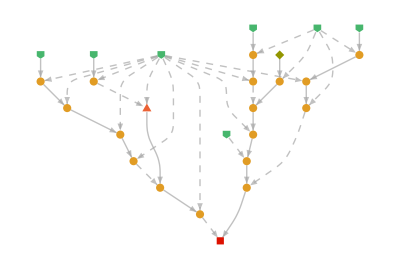

```mathematica
(*Obj[a,Cat[cC]]はcCという名前の圏のaという名前のオブジェクトという意味*)
(*Mor[f,Obj[a,Cat[cC]],Obj[b,Cat[cC]],Cat[cC]]はオブジェクトaからbへのfという名前の、圏cCの射という意味*)
MorUnionAxiom=ForAll[{f,g,a,b,c,cC},M[Mor[g,Obj[b,Cat[cC]],Obj[c,Cat[cC]],Cat[cC]],Mor[f,Obj[a,Cat[cC]],Obj[b,Cat[cC]],Cat[cC]]]==Mor[NameM[g,f,b],Obj[a,Cat[cC]],Obj[c,Cat[cC]],Cat[cC]]]
MorAssociativityAxiom=ForAll[{f,g,h,a,b,c,d,cC},M[M[Mor[f,Obj[c,Cat[cC]],Obj[d,Cat[cC]],Cat[cC]],Mor[g,Obj[b,Cat[cC]],Obj[c,Cat[cC]],Cat[cC]]],Mor[h,Obj[a,Cat[cC]],Obj[b,Cat[cC]],Cat[cC]]]==M[Mor[f,Obj[c,Cat[cC]],Obj[d,Cat[cC]],Cat[cC]],M[Mor[g,Obj[b,Cat[cC]],Obj[c,Cat[cC]],Cat[cC]],Mor[h,Obj[a,Cat[cC]],Obj[b,Cat[cC]],Cat[cC]]]]]

MorIdLeftAxiom=ForAll[{f,g,a,b,cC},M[Mor[Id[f],Obj[b,Cat[cC]],Obj[b,Cat[cC]],Cat[cC]],Mor[g,Obj[a,Cat[cC]],Obj[b,Cat[cC]],Cat[cC]]]==Mor[g,Obj[a,Cat[cC]],Obj[b,Cat[cC]],Cat[cC]]]
MorIdRightAxiom=ForAll[{f,g,a,b,cC},M[Mor[g,Obj[a,Cat[cC]],Obj[b,Cat[cC]],Cat[cC]],Mor[Id[f],Obj[a,Cat[cC]],Obj[a,Cat[cC]],Cat[cC]]]==Mor[g,Obj[a,Cat[cC]],Obj[b,Cat[cC]],Cat[cC]]]
MorAxioms={MorAssociativityAxiom,MorUnionAxiom,MorIdLeftAxiom,MorIdRightAxiom}

(*
複数の射の合成が同じである証明
ca=Obj[a,Cat[cC]]
cb=Obj[b,Cat[cC]]
cc=Obj[c,Cat[cC]]
cd=Obj[d,Cat[cC]]
ce=Obj[e,Cat[cC]]
cf=Mor[f,ca,cb,Cat[cC]]
cg=Mor[g,cb,cc,Cat[cC]]
ch=Mor[h,cc,cd,Cat[cC]]
ci=Mor[i,cd,ce,Cat[cC]]
Axiom={MorAxioms}
prop=M[M[M[ci,ch],cg],cf]==M[ci,M[ch,M[cg,cf]]]

proof=FindEquationalProof[prop,Axiom]
proof["ProofGraph"]
*)


(*恒等射は名前を変えても同じ
ca=Obj[a,Cat[cC]]
prop=Mor[Id[f],ca,ca,Cat[cC]]==Mor[Id[g],ca,ca,Cat[cC]]
Axiom={MorAxioms}
proof=FindEquationalProof[prop,Axiom]
proof["ProofGraph"]
*)


FunctorApplyObjAxiom=ForAll[{F,cC,cD,a},FO[Fun[F,Cat[cC],Cat[cD]],Obj[a,Cat[cC]]]==Obj[NameFO[F,a,cC],Cat[cD]]]
FunctorApplyMorAxiom=ForAll[{F,cC,cD,f,a,b},FA[Fun[F,Cat[cC],Cat[cD]],Mor[f,Obj[a,Cat[cC]],Obj[b,Cat[cC]],Cat[cC]]]==Mor[NameFA[F,f],Obj[NameFO[F,a,cC],Cat[cD]],Obj[NameFO[F,b,cC],Cat[cD]],Cat[cD]]]

FunctorApplyUnionMorAxiom=ForAll[{F,cC,cD,f,g,a,b,c},FA[Fun[F,Cat[cC],Cat[cD]],M[Mor[g,Obj[b,Cat[cC]],Obj[c,Cat[cC]],Cat[cC]],Mor[f,Obj[a,Cat[cC]],Obj[b,Cat[cC]],Cat[cC]]]]==M[Mor[NameFA[F,g],Obj[NameFO[F,b,cC],Cat[cD]],Obj[NameFO[F,c,cC],Cat[cD]],Cat[cD]],Mor[NameFA[F,f],Obj[NameFO[F,a,cC],Cat[cD]],Obj[NameFO[F,b,cC],Cat[cD]],Cat[cD]]]]
(*
合成射を分解する確認
Notation={Cat[cC]==A,Cat[cD]==B,Obj[a,Cat[cC]]==ca,Obj[b,Cat[cC]]==cb,Obj[c,Cat[cC]]==cc,NameFA[F,f]==Ff,NameFA[F,g]==Fg,Obj[NameFO[F,a,cC],Cat[cD]]==Fa,Obj[NameFO[F,b,cC],Cat[cD]]==Fb,Obj[NameFO[F,c,cC],Cat[cD]]==Fc}
Axiom={FunctorApplyUnionMorAxiom,Notation}
prop=FA[Fun[F,A,B],M[Mor[g,cb,cc,A],Mor[f,ca,cb,A]]]==M[Mor[Fg,Fb,Fc,B],Mor[Ff,Fa,Fb,B]]
proof=FindEquationalProof[prop,Axiom]
proof["ProofGraph"]
*)

FunctorApplyIdMorAxiom=ForAll[{F,cC,cD,f,a},FA[Fun[F,Cat[cC],Cat[cD]],Mor[Id[f],Obj[a,Cat[cC]],Obj[a,Cat[cC]],Cat[cC]]]==Mor[Id[NameFA[F,f]],Obj[NameFO[F,a,cC],Cat[cD]],Obj[NameFO[F,a,cC],Cat[cD]],Cat[cD]]]

(*
ちゃんと単位射を移して単位射になっているかの確認
Notation={Cat[cC]==A,Cat[cD]==B,Obj[a,Cat[cC]]==ca,Obj[NameFO[F,a,cC],Cat[cD]]==Fa,Obj[b,Cat[cD]]==db,Mor[g,Obj[NameFO[F,a,cC],Cat[cD]],Obj[b,Cat[cD]],Cat[cD]]==dg}
Axiom={MorAxioms,FunctorApplyObjAxiom,FunctorApplyMorAxiom,FunctorApplyUnionMorAxiom,FunctorApplyIdMorAxiom,Notation}
prop=M[dg,FA[Fun[F,A,B],Mor[Id[f],ca,ca,A]]]==dg
proof=FindEquationalProof[prop,Axiom]
proof["ProofGraph"]
*)

(*
MFへの射の適応とオブジェクトの適応を定義して、それらが関手となっていることを確かめる。
F:cC->cD,G:cD->cEとして、MFA[MF[G,F],a]=FA[G,FA[F,f]]と定義する。
*)

preFunctorUnionObjAxiom=ForAll[{F,G,cC,cD,cE,a},MFO[MF[Fun[G,Cat[cD],Cat[cE]],Fun[F,Cat[cC],Cat[cD]]],Obj[a,Cat[cC]]]==FO[Fun[G,Cat[cD],Cat[cE]],FO[Fun[F,Cat[cC],Cat[cD]],Obj[a,Cat[cC]]]]]

(*
ちゃんとcCのオブジェクトを飛ばすとcEのオブジェクトに飛ぶことを確かめる。
Axiom={preFunctorUnionObjAxiom,FunctorApplyObjAxiom}
prop=MFO[MF[Fun[G,Cat[cD],Cat[cE]],Fun[F,Cat[cC],Cat[cD]]],Obj[a,Cat[cC]]]==Obj[NameFO[G,NameFO[F,a,cC],cD],Cat[cE]]
proof=FindEquationalProof[prop,Axiom]
proof["ProofGraph"]
*)


preFunctorUnionMorAxiom=ForAll[{F,G,cC,cD,cE,f,a,b},MFA[MF[Fun[G,Cat[cD],Cat[cE]],Fun[F,Cat[cC],Cat[cD]]],Mor[f,Obj[a,Cat[cC]],Obj[b,Cat[cC]],Cat[cC]]]==FA[Fun[G,Cat[cD],Cat[cE]],FA[Fun[F,Cat[cC],Cat[cD]],Mor[f,Obj[a,Cat[cC]],Obj[b,Cat[cC]],Cat[cC]]]]]

(*
ちゃんとcCの射fを飛ばした先がcEの射になっていることを確認
Axiom={preFunctorUnionObjAxiom,preFunctorUnionMorAxiom,FunctorApplyObjAxiom,FunctorApplyMorAxiom}
prop=MFA[MF[Fun[G,Cat[cD],Cat[cE]],Fun[F,Cat[cC],Cat[cD]]],Mor[f,Obj[a,Cat[cC]],Obj[b,Cat[cC]],Cat[cC]]]==Mor[NameFA[G,NameFA[F,f]],Obj[NameFO[G,NameFO[F,a,cC],cD],Cat[cE]],Obj[NameFO[G,NameFO[F,b,cC],cD],Cat[cE]],Cat[cE]]
proof=FindEquationalProof[prop,Axiom]
proof["ProofGraph"]
*)


(*合成射を分解する事の確認
ca=Obj[a,Cat[cC]]
cb=Obj[b,Cat[cC]]
cc=Obj[c,Cat[cC]]
cf=Mor[f,ca,cb,Cat[cC]]
cg=Mor[g,cb,cc,Cat[cC]]
FF=Fun[F,Cat[cC],Cat[cD]]
FG=Fun[G,Cat[cD],Cat[cE]]
GF=MF[FG,FF]
GFg=MFA[GF,cg]
GFf=MFA[GF,cf]
prop=MFA[MF[FG,FF],M[cg,cf]]==M[GFg,GFf]
Axiom={MorAxioms,preFunctorUnionObjAxiom,preFunctorUnionMorAxiom,FunctorApplyObjAxiom,FunctorApplyMorAxiom,FunctorApplyUnionMorAxiom}
proof=FindEquationalProof[prop,Axiom]
proof["ProofGraph"]
*)



(*
単位射を単位射に移す事の証明
ca=Obj[a,Cat[cC]]
Idf=Mor[Id[f],ca,ca,Cat[cC]]
FF=Fun[F,Cat[cC],Cat[cD]]
FG=Fun[G,Cat[cD],Cat[cE]]
GF=MF[FG,FF]
GFIdf=MFA[GF,Idf]
GFa=MFO[GF,ca]

prop=GFIdf==Mor[Id[idName],GFa,GFa,Cat[cE]]
Axiom={MorAxioms,preFunctorUnionObjAxiom,preFunctorUnionMorAxiom,FunctorApplyObjAxiom,FunctorApplyMorAxiom,FunctorApplyIdMorAxiom}
proof=FindEquationalProof[prop,Axiom]
proof["ProofGraph"]
*)




FunctorUnionAxiom=ForAll[{F,G,cC,cD,cE},MF[Fun[G,Cat[cD],Cat[cE]],Fun[F,Cat[cC],Cat[cD]]]==Fun[NameMF[G,F,cD],Cat[cC],Cat[cE]]]

FunctorUnionObjAxiom=ForAll[{F,G,cC,cD,cE,a},FO[Fun[NameMF[G,F,cD],Cat[cC],Cat[cE]],Obj[a,Cat[cC]]]==FO[Fun[G,Cat[cD],Cat[cE]],FO[Fun[F,Cat[cC],Cat[cD]],Obj[a,Cat[cC]]]]]

FunctorUnionMorAxiom=ForAll[{F,G,cC,cD,cE,f,a,b},FA[Fun[NameMF[G,F,cD],Cat[cC],Cat[cE]],Mor[f,Obj[a,Cat[cC]],Obj[b,Cat[cC]],Cat[cC]]]==FA[Fun[G,Cat[cD],Cat[cE]],FA[Fun[F,Cat[cC],Cat[cD]],Mor[f,Obj[a,Cat[cC]],Obj[b,Cat[cC]],Cat[cC]]]]]

(*
関手の合成が結合法則を満たす事の証明
prop=FA[Fun[NameMF[NameMF[H,G,cE],F,cD],Cat[cC],Cat[cF]],Mor[f,Obj[a,Cat[cC]],Obj[b,Cat[cC]],Cat[cC]]]==FA[Fun[NameMF[H,NameMF[G,F,cD],cE],Cat[cC],Cat[cF]],Mor[f,Obj[a,Cat[cC]],Obj[b,Cat[cC]],Cat[cC]]]
Axiom={FunctorUnionAxiom,FunctorUnionObjAxiom,FunctorUnionMorAxiom,MorAxioms,FunctorApplyMorAxiom,FunctorApplyObjAxiom}
proof=FindEquationalProof[prop,Axiom]
proof["ProofGraph"]
*)



(*恒等関手について*)
IdFunctorApplyObjAxiom=ForAll[{F,cC,a},FO[Fun[Id[F],Cat[cC],Cat[cC]],Obj[a,Cat[cC]]]==Obj[a,Cat[cC]]]
IdFunctorApplyMorAxiom=ForAll[{F,cC,f,a,b},FA[Fun[Id[F],Cat[cC],Cat[cC]],Mor[f,Obj[a,Cat[cC]],Obj[b,Cat[cC]],Cat[cC]]]==Mor[f,Obj[a,Cat[cC]],Obj[b,Cat[cC]],Cat[cC]]]
IdFunctorUnionAxiom=ForAll[{F,G,cC,cD},(MF[Fun[G,Cat[cC],Cat[cD]],Fun[Id[F],Cat[cC],Cat[cC]]]==Fun[G,Cat[cC],Cat[cD]])&&(MF[Fun[Id[F],Cat[cD],Cat[cD]],Fun[G,Cat[cC],Cat[cD]]]==Fun[G,Cat[cC],Cat[cD]])]
IdFunctorAxioms={IdFunctorApplyObjAxiom,IdFunctorApplyMorAxiom,IdFunctorUnionAxiom}


(*反変関手について*)

OpFunctorApplyObjAxiom=ForAll[{F,cC,cD,a},OFO[OFun[F,Cat[cC],Cat[cD]],Obj[a,Cat[cC]]]==Obj[NameOFO[F,a,cC],Cat[cD]]]

OpFunctorApplyMorAxiom=ForAll[{F,cC,cD,f,a,b},OFA[OFun[F,Cat[cC],Cat[cD]],Mor[f,Obj[a,Cat[cC]],Obj[b,Cat[cC]],Cat[cC]]]==Mor[NameOFA[F,f],Obj[NameOFO[F,b,cC],Cat[cD]],Obj[NameOFO[F,a,cC],Cat[cD]],Cat[cD]]]

OpFunctorApplyUnionMorAxiom=ForAll[{F,cC,cD,f,g,a,b,c},OFA[OFun[F,Cat[cC],Cat[cD]],M[Mor[g,Obj[b,Cat[cC]],Obj[c,Cat[cC]],Cat[cC]],Mor[f,Obj[a,Cat[cC]],Obj[b,Cat[cC]],Cat[cC]]]]==M[Mor[NameOFA[F,f],Obj[NameOFO[F,b,cC],Cat[cD]],Obj[NameOFO[F,a,cC],Cat[cD]],Cat[cD]],Mor[NameOFA[F,g],Obj[NameOFO[F,c,cC],Cat[cD]],Obj[NameOFO[F,b,cC],Cat[cD]],Cat[cD]]]]

OpFunctorApplyIdMorAxiom=ForAll[{F,cC,cD,f,a},OFA[OFun[F,Cat[cC],Cat[cD]],Mor[Id[f],Obj[a,Cat[cC]],Obj[a,Cat[cC]],Cat[cC]]]==Mor[Id[NameOFA[F,f]],Obj[NameOFO[F,a,cC],Cat[cD]],Obj[NameOFO[F,a,cC],Cat[cD]],Cat[cD]]]

(*反変関手を含む関手の合成は明示的には定義しない。(段階的に適応する形で書けば良いので)*)

FunctorAxioms={FunctorApplyObjAxiom,FunctorApplyMorAxiom,FunctorApplyIdMorAxiom,FunctorApplyUnionMorAxiom,FunctorUnionAxiom,FunctorUnionObjAxiom,FunctorUnionMorAxiom,IdFunctorAxioms,OpFunctorApplyMorAxiom,OpFunctorApplyObjAxiom,OpFunctorApplyUnionMorAxiom,OpFunctorApplyIdMorAxiom}


(*自然変換の可換性の公理*)
NatApplyAxiom=ForAll[{Al,F,G,cC,cD,a},NA[Nat[Al,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cC],Cat[cD]]],Obj[a,Cat[cC]]]==Mor[NameNA[Al,a],Obj[NameFO[F,a,cC],Cat[cD]],Obj[NameFO[G,a,cC],Cat[cD]],Cat[cD]]]
NatAxiom=ForAll[{Al,F,G,cC,cD,f,a,b},M[FA[Fun[G,Cat[cC],Cat[cD]],Mor[f,Obj[a,Cat[cC]],Obj[b,Cat[cC]],Cat[cC]]],NA[Nat[Al,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cC],Cat[cD]]],Obj[a,Cat[cC]]]]==M[NA[Nat[Al,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cC],Cat[cD]]],Obj[b,Cat[cC]]],FA[Fun[F,Cat[cC],Cat[cD]],Mor[f,Obj[a,Cat[cC]],Obj[b,Cat[cC]],Cat[cC]]]]]

(*NatAxiomがちゃんとできているかのテスト
Notation={Cat[cC]==A,Cat[cD]==B,Obj[a,Cat[cC]]==ca,Obj[b,Cat[cC]]==cb,Mor[f,ca,cb,Cat[cC]]==cf,Fun[F,A,B]==FF,Fun[G,A,B]==FG,Nat[Al,FF,FG]==NAl}
prop=M[FA[FG,cf],NA[NAl,ca]]==M[NA[NAl,cb],FA[FF,cf]]

Axiom={NatApplyAxiom,NatAxiom,Notation}
proof=FindEquationalProof[prop,Axiom]
proof["ProofGraph"]
*)


(*垂直合成へのオブジェクトの適応*)
preVNMApplyAxiom=ForAll[{Al,Be,F,G,H,cC,cD,a},VNMA[VNM[Nat[Be,Fun[G,Cat[cC],Cat[cD]],Fun[H,Cat[cC],Cat[cD]]],Nat[Al,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cC],Cat[cD]]]],Obj[a,Cat[cC]]]==M[NA[Nat[Be,Fun[G,Cat[cC],Cat[cD]],Fun[H,Cat[cC],Cat[cD]]],Obj[a,Cat[cC]]],NA[Nat[Al,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cC],Cat[cD]]],Obj[a,Cat[cC]]]]]


(*
(*垂直合成が自然変換の公理を満たすことを確かめる*)
ca=Obj[a,Cat[cC]]
cb=Obj[b,Cat[cC]]
cf=Mor[f,ca,cb,Cat[cC]]
FF=Fun[F,Cat[cC],Cat[cD]]
FG=Fun[G,Cat[cC],Cat[cD]]
FH=Fun[H,Cat[cC],Cat[cD]]
Ff=FA[FF,cf]
Gf=FA[FG,cf]
Hf=FA[FH,cf]
NAl=Nat[Al,FF,FG]
Ala=NA[NAl,ca]
Alb=NA[NAl,cb]
NBe=Nat[Be,FG,FH]
Bea=NA[NBe,ca]
Beb=NA[NBe,cb]

prop=M[Hf,VNMA[VNM[NBe,NAl],ca]]==M[VNMA[VNM[NBe,NAl],cb],Ff]

(*VNMAを展開してMの順序変更*)
lemma1=M[Hf,VNMA[VNM[NBe,NAl],ca]]==M[M[Hf,NA[NBe,ca]],Ala]
(*右側の自然性*)
lemma2=M[M[Hf,Bea],Ala]==M[M[Beb,Gf],Ala]

(*Mの順序変更と左の自然性*)

lemma3=M[M[Beb,Gf],Ala]==M[M[Beb,Alb],Ff]

(*VNMAの定義でくくる*)
lemma4=M[M[Beb,Alb],Ff]==M[VNMA[VNM[NBe,NAl],cb],Ff]

Axiom={NatApplyAxiom,NatAxiom,MorAxioms,FunctorAxioms,preVNMApplyAxiom}
proof1=FindEquationalProof[lemma1,Axiom]
proof1["ProofGraph"]
proof2=FindEquationalProof[lemma2,Axiom]
proof2["ProofGraph"]
proof3=FindEquationalProof[lemma3,Axiom]
proof3["ProofGraph"]
proof4=FindEquationalProof[lemma4,Axiom]
proof4["ProofGraph"]

proof=FindEquationalProof[prop,{lemma1,lemma2,lemma3,lemma4}]
proof["ProofGraph"]
*)



(*VNMが自然変換であることがわかったので、自然変換として定義する*)
VNMAxiom=ForAll[{Al,Be,F,G,H,cC,cD},VNM[Nat[Be,Fun[G,Cat[cC],Cat[cD]],Fun[H,Cat[cC],Cat[cD]]],Nat[Al,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cC],Cat[cD]]]]==Nat[NameVNM[Be,Al,G],Fun[F,Cat[cC],Cat[cD]],Fun[H,Cat[cC],Cat[cD]]]]
VNMApplyAxiom=ForAll[{Al,Be,F,G,H,cC,cD,a},NA[VNM[Nat[Be,Fun[G,Cat[cC],Cat[cD]],Fun[H,Cat[cC],Cat[cD]]],Nat[Al,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cC],Cat[cD]]]],Obj[a,Cat[cC]]]==M[NA[Nat[Be,Fun[G,Cat[cC],Cat[cD]],Fun[H,Cat[cC],Cat[cD]]],Obj[a,Cat[cC]]],NA[Nat[Al,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cC],Cat[cD]]],Obj[a,Cat[cC]]]]]

(*水平合成への適応の定義*)
(*水平合成の定義のための可換図式
ca=Obj[a,Cat[cC]]
FF=Fun[F,Cat[cC],Cat[cD]]
Fa=FO[FF,ca]
Ga=FO[FG,ca]
FG=Fun[G,Cat[cC],Cat[cD]]
FFp=Fun[Fp,Cat[cD],Cat[cE]]
FGp=Fun[Gp,Cat[cD],Cat[cE]]
NAl=Nat[Al,FF,FG]
Ala=NA[NAl,ca]
NBe=Nat[Be,FFp,FGp]

Notation={Ala==Mor[f,Obj[ad,Cat[cD]],Obj[bd,Cat[cD]],Cat[cD]],Fa==Obj[ad,Cat[cD]],Ga==Obj[bd,Cat[cD]]}
prop=M[NA[NBe,Ga],FA[FFp,Ala]]==M[FA[FGp,Ala],NA[NBe,Fa]]
Axiom={Notation,NatAxiom}
proof=FindEquationalProof[prop,Axiom]
proof["ProofGraph"]
*)


preHNMApplyAxiom=ForAll[{Al,Be,F,G,Fp,Gp,cC,cD,cE,a},(HNMA[HNM[Nat[Be,Fun[Fp,Cat[cD],Cat[cE]],Fun[Gp,Cat[cD],Cat[cE]]],Nat[Al,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cC],Cat[cD]]]],Obj[a,Cat[cC]]]==M[NA[Nat[Be,Fun[Fp,Cat[cD],Cat[cE]],Fun[Gp,Cat[cD],Cat[cE]]],FO[Fun[G,Cat[cC],Cat[cD]],Obj[a,Cat[cC]]]],FA[Fun[Fp,Cat[cD],Cat[cE]],NA[Nat[Al,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cC],Cat[cD]]],Obj[a,Cat[cC]]]]])&&(HNMA[HNM[Nat[Be,Fun[Fp,Cat[cD],Cat[cE]],Fun[Gp,Cat[cD],Cat[cE]]],Nat[Al,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cC],Cat[cD]]]],Obj[a,Cat[cC]]]==M[FA[Fun[Gp,Cat[cD],Cat[cE]],NA[Nat[Al,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cC],Cat[cD]]],Obj[a,Cat[cC]]]],NA[Nat[Be,Fun[Fp,Cat[cD],Cat[cE]],Fun[Gp,Cat[cD],Cat[cE]]],FO[Fun[F,Cat[cC],Cat[cD]],Obj[a,Cat[cC]]]]])]

(*水平合成の自然性
ca=Obj[a,Cat[cC]]
cb=Obj[b,Cat[cC]]
cf=Mor[f,ca,cb,Cat[cC]]
FF=Fun[F,Cat[cC],Cat[cD]]
FG=Fun[G,Cat[cC],Cat[cD]]
FFp=Fun[Fp,Cat[cD],Cat[cE]]
FGp=Fun[Gp,Cat[cD],Cat[cE]]
NBe=Nat[Be,FFp,FGp]
NAl=Nat[Al,FF,FG]

(*左側の可換性*)
prop1=M[FA[FG,cf],NA[NAl,ca]]==M[NA[NAl,cb],FA[FF,cf]]
(*右側の可換性*)
prop2=M[FA[FGp,Mor[f,Obj[a,Cat[cD]],Obj[b,Cat[cD]],Cat[cD]]],NA[NBe,Obj[a,Cat[cD]]]]==M[NA[NBe,Obj[b,Cat[cD]]],FA[FFp,Mor[f,Obj[a,Cat[cD]],Obj[b,Cat[cD]],Cat[cD]]]]
Axiom={NatAxiom}
proof1=FindEquationalProof[prop1,Axiom]
proof1["ProofGraph"]
proof2=FindEquationalProof[prop2,Axiom]
proof2["ProofGraph"]
*)




HNMAxiom=ForAll[{Al,Be,F,G,Fp,Gp,cC,cD,cE,a},HNM[Nat[Be,Fun[Fp,Cat[cD],Cat[cE]],Fun[Gp,Cat[cD],Cat[cE]]],Nat[Al,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cC],Cat[cD]]]]==Nat[NameHNM[Be,Al],MF[Fun[Fp,Cat[cD],Cat[cE]],Fun[F,Cat[cC],Cat[cD]]],MF[Fun[Gp,Cat[cD],Cat[cE]],Fun[G,Cat[cC],Cat[cD]]]]]

HNMApplyAxiom=ForAll[{Al,Be,F,G,Fp,Gp,cC,cD,cE,a},(NA[HNM[Nat[Be,Fun[Fp,Cat[cD],Cat[cE]],Fun[Gp,Cat[cD],Cat[cE]]],Nat[Al,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cC],Cat[cD]]]],Obj[a,Cat[cC]]]==M[NA[Nat[Be,Fun[Fp,Cat[cD],Cat[cE]],Fun[Gp,Cat[cD],Cat[cE]]],FO[Fun[G,Cat[cC],Cat[cD]],Obj[a,Cat[cC]]]],FA[Fun[Fp,Cat[cD],Cat[cE]],NA[Nat[Al,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cC],Cat[cD]]],Obj[a,Cat[cC]]]]])&&(NA[HNM[Nat[Be,Fun[Fp,Cat[cD],Cat[cE]],Fun[Gp,Cat[cD],Cat[cE]]],Nat[Al,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cC],Cat[cD]]]],Obj[a,Cat[cC]]]==M[FA[Fun[Gp,Cat[cD],Cat[cE]],NA[Nat[Al,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cC],Cat[cD]]],Obj[a,Cat[cC]]]],NA[Nat[Be,Fun[Fp,Cat[cD],Cat[cE]],Fun[Gp,Cat[cD],Cat[cE]]],FO[Fun[F,Cat[cC],Cat[cD]],Obj[a,Cat[cC]]]]])]

(*恒等変換*)
IdNatAxiom={ForAll[{Al,F,a,cC,cD},NA[Nat[Id[Al],Fun[F,Cat[cC],Cat[cD]],Fun[F,Cat[cC],Cat[cD]]],Obj[a,Cat[cC]]]==FA[Fun[F,Cat[cC],Cat[cD]],Mor[Id[cC],Obj[a,Cat[cC]],Obj[a,Cat[cC]],Cat[cC]]]],ForAll[{Al,F,G,cC,cD,IdName1,IdName2},(VNM[Nat[Id[IdName1],Fun[G,Cat[cC],Cat[cD]],Fun[G,Cat[cC],Cat[cD]]],Nat[Al,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cC],Cat[cD]]]]==Nat[Al,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cC],Cat[cD]]])&&(VNM[Nat[Al,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cC],Cat[cD]]],Nat[Id[IdName2],Fun[F,Cat[cC],Cat[cD]],Fun[F,Cat[cC],Cat[cD]]]]==Nat[Al,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cC],Cat[cD]]])]}

NatAxioms={NatApplyAxiom,NatAxiom,VNMAxiom,VNMApplyAxiom,HNMAxiom,HNMApplyAxiom,IdNatAxiom}




(*合成写像への値の適応*)
MapApplyAxiom=ForAll[{g,f,a,b,c,e},A[M[Mor[g,Obj[b,Cat[cSet]],Obj[c,Cat[cSet]],Cat[cSet]],Mor[f,Obj[a,Cat[cSet]],Obj[b,Cat[cSet]],Cat[cSet]]],Ele[e,Obj[a,Cat[cSet]]]]==A[Mor[g,Obj[b,Cat[cSet]],Obj[c,Cat[cSet]],Cat[cSet]],A[Mor[f,Obj[a,Cat[cSet]],Obj[b,Cat[cSet]],Cat[cSet]],Ele[e,Obj[a,Cat[cSet]]]]]]
MapApplyEleAxiom=ForAll[{f,a,b,x},A[Mor[f,Obj[a,Cat[cSet]],Obj[b,Cat[cSet]],Cat[cSet]],Ele[x,Obj[a,Cat[cSet]]]]==Ele[MapA[f,x,a],Obj[b,Cat[cSet]]]]
MapApplyIdAxiom=ForAll[{f,a,b,x},A[Mor[Id[f],Obj[a,Cat[cSet]],Obj[b,Cat[cSet]],Cat[cSet]],Ele[x,Obj[a,Cat[cSet]]]]==Ele[x,Obj[a,Cat[cSet]]]]
MapAxioms={MapApplyAxiom,MapApplyEleAxiom,MapApplyIdAxiom}

(*Homの公理*)
preHomRApplyObjAxiom=ForAll[{d,a,cC},HRO[HomR[Obj[d,Cat[cC]]],Obj[a,Cat[cC]]]==Obj[HomO[d,a,cC],Cat[cSet]]]
preHomRApplyMorAxiom=ForAll[{d,f,a,b,cC},HRA[HomR[Obj[d,Cat[cC]]],Mor[f,Obj[a,Cat[cC]],Obj[b,Cat[cC]],Cat[cC]]]==Mor[HomRA[d,f],Obj[HomO[d,a,cC],Cat[cSet]],Obj[HomO[d,b,cC],Cat[cSet]],Cat[cSet]]]
HomEleAxiom=ForAll[{d,a,e,cC},Ele[e,Obj[HomO[d,a,cC],Cat[cSet]]]==Mor[e,Obj[d,Cat[cC]],Obj[a,Cat[cC]],Cat[cC]]]
preHomRAxiom=ForAll[{d,f,a,b,cC,h},A[HRA[HomR[Obj[d,Cat[cC]]],Mor[f,Obj[a,Cat[cC]],Obj[b,Cat[cC]],Cat[cC]]],Ele[h,Obj[HomO[d,a,cC],Cat[cSet]]]]==M[Mor[f,Obj[a,Cat[cC]],Obj[b,Cat[cC]],Cat[cC]],Mor[h,Obj[d,Cat[cC]],Obj[a,Cat[cC]],Cat[cC]]]]

(*Homの確認
Notation={Obj[d,Cat[cC]]==cd,Obj[a,Cat[cC]]==ca,Obj[b,Cat[cC]]==cb,Mor[f,ca,cb,Cat[cC]]==cf}
(*Hom[c,f]が射である証明*)
prop1=HRA[HomR[cd],cf]==Mor[HomRA[d,f],Obj[HomO[d,a,cC],Cat[cSet]],Obj[HomO[d,b,cC],Cat[cSet]],Cat[cSet]]
(*Hom[c,f]にhを写像として適応すると射の合成fhとなる*)
prop2=A[HRA[HomR[cd],cf],Mor[h,Obj[d,Cat[cC]],Obj[a,Cat[cC]],Cat[cC]]]==M[cf,Mor[h,Obj[d,Cat[cC]],Obj[a,Cat[cC]],Cat[cC]]]

Axiom={Notation,preHomRApplyObjAxiom,preHomRApplyMorAxiom,HomEleAxiom,preHomRAxiom,MapApplyAxiom}
proof=FindEquationalProof[prop2,Axiom]
*)

(*Homの関手性（合成射の分解）
cd=Obj[d,Cat[cC]]
ca=Obj[a,Cat[cC]]
cb=Obj[b,Cat[cC]]
cc=Obj[c,Cat[cC]]
cf=Mor[f,Obj[a,Cat[cC]],Obj[b,Cat[cC]],Cat[cC]]
cg=Mor[g,Obj[b,Cat[cC]],Obj[c,Cat[cC]],Cat[cC]]
ch=Mor[h,Obj[d,Cat[cC]],Obj[a,Cat[cC]],Cat[cC]]

(*目的のやつ*)
LeftT=A[HRA[HomR[cd],M[cg,cf]],ch]
RightT=A[M[HRA[HomR[cd],cg],HRA[HomR[cd],cf]],ch]
prop=LeftT==RightT

Axiom={Notation,MapApplyAxiom,preHomRApplyObjAxiom,preHomRApplyMorAxiom,HomEleAxiom,preHomRAxiom,MorAxioms}
proof=FindEquationalProof[prop,Axiom]
proof["ProofGraph"]
*)


(*HomLの公理*)
preHomLApplyObjAxiom=ForAll[{d,a,cC},HLO[HomL[Obj[d,Cat[cC]]],Obj[a,Cat[cC]]]==Obj[HomO[a,d,cC],Cat[cSet]]]

preHomLApplyMorAxiom=ForAll[{d,f,a,b,cC},HLA[HomL[Obj[d,Cat[cC]]],Mor[f,Obj[a,Cat[cC]],Obj[b,Cat[cC]],Cat[cC]]]==Mor[HomLA[f,d],Obj[HomO[b,d,cC],Cat[cSet]],Obj[HomO[a,d,cC],Cat[cSet]],Cat[cSet]]]

preHomLAxiom=ForAll[{d,f,a,b,cC,h},A[HLA[HomL[Obj[d,Cat[cC]]],Mor[f,Obj[a,Cat[cC]],Obj[b,Cat[cC]],Cat[cC]]],Ele[h,Obj[HomO[b,d,cC],Cat[cSet]]]]==M[Mor[h,Obj[b,Cat[cC]],Obj[d,Cat[cC]],Cat[cC]],Mor[f,Obj[a,Cat[cC]],Obj[b,Cat[cC]],Cat[cC]]]]

(*
(*HomLが反変関手（合成射の分解）*)
cd=Obj[d,Cat[cC]]
ca=Obj[a,Cat[cC]]
cb=Obj[b,Cat[cC]]
cc=Obj[c,Cat[cC]]
cf=Mor[f,Obj[a,Cat[cC]],Obj[b,Cat[cC]],Cat[cC]]
cg=Mor[g,Obj[b,Cat[cC]],Obj[c,Cat[cC]],Cat[cC]]
ch=Mor[h,Obj[c,Cat[cC]],Obj[d,Cat[cC]],Cat[cC]]

(*目的のやつ*)
LeftT=A[HLA[HomL[cd],M[cg,cf]],ch]
RightT=A[M[HLA[HomL[cd],cf],HLA[HomL[cd],cg]],ch]
prop=LeftT==RightT
Axiom={MapApplyAxiom,preHomLApplyObjAxiom,preHomLApplyMorAxiom,HomEleAxiom,preHomLAxiom,MorAxioms}
proof=FindEquationalProof[prop,Axiom]
proof["ProofGraph"]
*)


(*HomRとHomLへの適応を看守への適応として定義する*)
HomRFunctorAxiom={ForAll[{d,cC},HomR[Obj[d,Cat[cC]]]==Fun[HomRF[d],Cat[cC],Cat[cSet]]]}
HomRApplyObjAxiom=ForAll[{d,a,cC},FO[HomR[Obj[d,Cat[cC]]],Obj[a,Cat[cC]]]==Obj[HomO[d,a,cC],Cat[cSet]]]
HomRApplyMorAxiom=ForAll[{d,f,a,b,cC},FA[HomR[Obj[d,Cat[cC]]],Mor[f,Obj[a,Cat[cC]],Obj[b,Cat[cC]],Cat[cC]]]==Mor[HomRA[d,f],Obj[HomO[d,a,cC],Cat[cSet]],Obj[HomO[d,b,cC],Cat[cSet]],Cat[cSet]]]
HomRAxiom=ForAll[{d,f,a,b,cC,h},A[FA[HomR[Obj[d,Cat[cC]]],Mor[f,Obj[a,Cat[cC]],Obj[b,Cat[cC]],Cat[cC]]],Ele[h,Obj[HomO[d,a,cC],Cat[cSet]]]]==M[Mor[f,Obj[a,Cat[cC]],Obj[b,Cat[cC]],Cat[cC]],Mor[h,Obj[d,Cat[cC]],Obj[a,Cat[cC]],Cat[cC]]]]

HomLOpFunctorAxiom={ForAll[{d,cC},HomL[Obj[d,Cat[cC]]]==OFun[HomLF[d],Cat[cC],Cat[cSet]]]}
HomLApplyObjAxiom=ForAll[{d,a,cC},OFO[HomL[Obj[d,Cat[cC]]],Obj[a,Cat[cC]]]==Obj[HomO[a,d,cC],Cat[cSet]]]

HomLApplyMorAxiom=ForAll[{d,f,a,b,cC},OFA[HomL[Obj[d,Cat[cC]]],Mor[f,Obj[a,Cat[cC]],Obj[b,Cat[cC]],Cat[cC]]]==Mor[HomLA[f,d],Obj[HomO[b,d,cC],Cat[cSet]],Obj[HomO[a,d,cC],Cat[cSet]],Cat[cSet]]]

HomLAxiom=ForAll[{d,f,a,b,cC,h},A[OFA[HomL[Obj[d,Cat[cC]]],Mor[f,Obj[a,Cat[cC]],Obj[b,Cat[cC]],Cat[cC]]],Ele[h,Obj[HomO[b,d,cC],Cat[cSet]]]]==M[Mor[h,Obj[b,Cat[cC]],Obj[d,Cat[cC]],Cat[cC]],Mor[f,Obj[a,Cat[cC]],Obj[b,Cat[cC]],Cat[cC]]]]

HomAxioms={HomRFunctorAxiom,HomRApplyObjAxiom,HomRApplyMorAxiom,HomRAxiom,HomLOpFunctorAxiom,HomLApplyObjAxiom,HomLApplyMorAxiom,HomLAxiom,HomEleAxiom}

(*Homを用いた随伴の公理*)
AdjMorAxiom=ForAll[{Ad,F,G,cC,cD,a,b},AA[Adj[Ad,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cD],Cat[cC]]],Obj[a,Cat[cC]],Obj[b,Cat[cD]]]==Mor[NameAdj[Ad,a,b],Obj[HomO[NameFO[F,a,cC],b,cD],Cat[cSet]],Obj[HomO[a,NameFO[G,b,cD],cC],Cat[cSet]],Cat[cSet]]]

AdjAxiom=ForAll[{Ad,F,G,f,g,a,b,ap,bp,cC,cD},(M[FA[HomR[Obj[a,Cat[cC]]],FA[Fun[G,Cat[cD],Cat[cC]],Mor[g,Obj[b,Cat[cD]],Obj[bp,Cat[cD]],Cat[cD]]]],AA[Adj[Ad,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cD],Cat[cC]]],Obj[a,Cat[cC]],Obj[b,Cat[cD]]]]==M[AA[Adj[Ad,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cD],Cat[cC]]],Obj[a,Cat[cC]],Obj[bp,Cat[cD]]],FA[HomR[FO[Fun[F,Cat[cC],Cat[cD]],Obj[a,Cat[cC]]]],Mor[g,Obj[b,Cat[cD]],Obj[bp,Cat[cD]],Cat[cD]]]])&&(M[AA[Adj[Ad,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cD],Cat[cC]]],Obj[a,Cat[cC]],Obj[b,Cat[cD]]],OFA[HomL[Obj[b,Cat[cD]]],FA[Fun[F,Cat[cC],Cat[cD]],Mor[f,Obj[a,Cat[cC]],Obj[ap,Cat[cC]],Cat[cC]]]]]==M[OFA[HomL[FO[Fun[G,Cat[cD],Cat[cC]],Obj[b,Cat[cD]]]],Mor[f,Obj[a,Cat[cC]],Obj[ap,Cat[cC]],Cat[cC]]],AA[Adj[Ad,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cD],Cat[cC]]],Obj[ap,Cat[cC]],Obj[b,Cat[cD]]]])]


(*随伴の公理の確認（共変の方）
ca=Obj[a,Cat[cC]]
db=Obj[b,Cat[cD]]
dbp=Obj[bp,Cat[cD]]
df=Mor[f,db,dbp,Cat[cD]]
FG=Fun[G,Cat[cD],Cat[cC]]
Gf=FA[FG,df]
Gb=FO[FG,db]
Gbp=FO[FG,dbp]
FF=Fun[F,Cat[cC],Cat[cD]]
Fa=FO[FF,ca]
AAd=Adj[Ad,FF,FG]
Adab=AA[AAd,ca,db]
Adabp=AA[AAd,ca,dbp]
prop=M[FA[HomR[ca],Gf],Adab]==M[Adabp,FA[HomR[Fa],df]]
Axiom={AdjMorAxiom,AdjAxiom}
proof=FindEquationalProof[prop,Axiom]
proof["ProofGraph"]
*)

(*随伴の公理の確認（反変の方）
ca=Obj[a,Cat[cC]]
db=Obj[b,Cat[cD]]
cap=Obj[ap,Cat[cC]]
cf=Mor[f,ca,cap,Cat[cC]]
FG=Fun[G,Cat[cD],Cat[cC]]
FF=Fun[F,Cat[cC],Cat[cD]]
Fa=FO[FF,ca]
Fap=FO[FF,cap]
Ff=FA[FF,cf]
Gb=FO[FG,db]
AAd=Adj[Ad,FF,FG]
Adab=AA[AAd,ca,db]
Adapb=AA[AAd,cap,db]
prop=M[Adab,OFA[HomL[db],Ff]]==M[OFA[HomL[Gb],cf],Adapb]
Axiom={AdjMorAxiom,AdjAxiom}
proof=FindEquationalProof[prop,Axiom]
proof["ProofGraph"]
*)

(*随伴の全単射の逆写像を定義*)
InvAdjMorAxiom=ForAll[{Ad,F,G,cC,cD,a,b},AA[Adj[Inv[Ad],Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cD],Cat[cC]]],Obj[a,Cat[cC]],Obj[b,Cat[cD]]]==Mor[NameAdj[Inv[Ad],a,b],Obj[HomO[a,NameFO[G,b,cD],cC],Cat[cSet]],Obj[HomO[NameFO[F,a,cC],b,cD],Cat[cSet]],Cat[cSet]]]

InvAdjUnionAxiom=ForAll[{Ad,F,G,IdName,cC,cD,a,b},(M[AA[Adj[Ad,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cD],Cat[cC]]],Obj[a,Cat[cC]],Obj[b,Cat[cD]]],AA[Adj[Inv[Ad],Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cD],Cat[cC]]],Obj[a,Cat[cC]],Obj[b,Cat[cD]]]]==Mor[Id[IdName],FO[HomR[Obj[a,Cat[cC]]],FO[Fun[G,Cat[cD],Cat[cC]],Obj[b,Cat[cD]]]],FO[HomR[Obj[a,Cat[cC]]],FO[Fun[G,Cat[cD],Cat[cC]],Obj[b,Cat[cD]]]],Cat[cSet]])&&(M[AA[Adj[Inv[Ad],Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cD],Cat[cC]]],Obj[a,Cat[cC]],Obj[b,Cat[cD]]],AA[Adj[Ad,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cD],Cat[cC]]],Obj[a,Cat[cC]],Obj[b,Cat[cD]]]]==Mor[Id[IdName],FO[HomR[FO[Fun[F,Cat[cC],Cat[cD]],Obj[a,Cat[cC]]]],Obj[b,Cat[cD]]],FO[HomR[FO[Fun[F,Cat[cC],Cat[cD]],Obj[a,Cat[cC]]]],Obj[b,Cat[cD]]],Cat[cSet]])]


InvAdjAxiom=ForAll[{Ad,F,G,f,g,a,b,ap,bp,cC,cD},(M[FA[HomR[FO[Fun[F,Cat[cC],Cat[cD]],Obj[a,Cat[cC]]]],Mor[g,Obj[b,Cat[cD]],Obj[bp,Cat[cD]],Cat[cD]]],AA[Adj[Inv[Ad],Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cD],Cat[cC]]],Obj[a,Cat[cC]],Obj[b,Cat[cD]]]]==M[AA[Adj[Inv[Ad],Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cD],Cat[cC]]],Obj[a,Cat[cC]],Obj[bp,Cat[cD]]],FA[HomR[Obj[a,Cat[cC]]],FA[Fun[G,Cat[cD],Cat[cC]],Mor[g,Obj[b,Cat[cD]],Obj[bp,Cat[cD]],Cat[cD]]]]])&&(M[AA[Adj[Inv[Ad],Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cD],Cat[cC]]],Obj[a,Cat[cC]],Obj[b,Cat[cD]]],OFA[HomL[FO[Fun[G,Cat[cD],Cat[cC]],Obj[b,Cat[cD]]]],Mor[f,Obj[a,Cat[cC]],Obj[ap,Cat[cC]],Cat[cC]]]]==M[OFA[HomL[Obj[b,Cat[cD]]],FA[Fun[F,Cat[cC],Cat[cD]],Mor[f,Obj[a,Cat[cC]],Obj[ap,Cat[cC]],Cat[cC]]]],AA[Adj[Inv[Ad],Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cD],Cat[cC]]],Obj[ap,Cat[cC]],Obj[b,Cat[cD]]]])]

AdjAxioms={AdjMorAxiom,AdjAxiom,InvAdjMorAxiom,InvAdjAxiom,InvAdjUnionAxiom}

(*Unitへのオブジェクトの適応*)
preAdjUnitAxiom=ForAll[{eta,Ad,F,G,cC,cD,a,b,IdName},UA[Unit[eta,Adj[Ad,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cD],Cat[cC]]]],Obj[a,Cat[cC]]]==A[AA[Adj[Ad,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cD],Cat[cC]]],Obj[a,Cat[cC]],FO[Fun[F,Cat[cC],Cat[cD]],Obj[a,Cat[cC]]]],Mor[Id[IdName],FO[Fun[F,Cat[cC],Cat[cD]],Obj[a,Cat[cC]]],FO[Fun[F,Cat[cC],Cat[cD]],Obj[a,Cat[cC]]],Cat[cD]]]]

(*Unitの自然性
ca=Obj[a,Cat[cC]]
cb=Obj[b,Cat[cC]]
cf=Mor[f,ca,cb,Cat[cC]]
FF=Fun[F,Cat[cC],Cat[cD]]
FG=Fun[G,Cat[cD],Cat[cC]]
GFf=FA[MF[FG,FF],cf]
GFb=FO[MF[FG,FF],cb]
Fa=FO[Fun[F,Cat[cC],Cat[cD]],ca]
ObjFa=Obj[NameFO[F,a,cC],Cat[cD]]
Fb=FO[Fun[F,Cat[cC],Cat[cD]],cb]
ObjFa=Obj[NameFO[F,a,cC],Cat[cD]]
Ff=FA[FF,cf]
MorFf=Mor[NameFA[F,f],Obj[NameFO[F,a,cC],Cat[cD]],Obj[NameFO[F,b,cC],Cat[cD]],Cat[cD]]
MorGFf=Mor[NameFA[NameMF[G,F,cD],f],Obj[NameFO[NameMF[G,F,cD],a,cC],Cat[cC]],Obj[NameFO[NameMF[G,F,cD],b,cC],Cat[cC]],Cat[cC]]
dIdFa=Mor[Id[IdFa],Fa,Fa,Cat[cD]]
dIdFb=Mor[Id[IdFb],Fb,Fb,Cat[cD]]
AAd=Adj[Ad,FF,FG]
AdaFa=AA[AAd,ca,Fa]
AdaFb=AA[AAd,ca,Fb]
AdbFa=AA[AAd,cb,Fa]
AdbFb=AA[AAd,cb,Fb]
HomFfFa=OFA[HomL[Fa],Ff]
HomfGFb=OFA[HomL[GFb],cf]
HomFaFa=Obj[HomO[NameFO[F,a,cC],NameFO[F,a,cC],cD],Cat[cSet]]
HomaGFa=Obj[HomO[a,NameFO[G,NameFO[F,a,cC],cD],cC],Cat[cSet]]
HomFaFf=FA[HomR[Fa],Ff]
HomFa=HomR[Fa]
FunHomFa=Fun[HomRF[NameFO[F,a,cC]],Cat[cD],Cat[cSet]]
MorHomFaFf=Mor[NameFA[HomRF[NameFO[F,a,cC]],NameFA[F,f]],Obj[HomO[NameFO[F,a,cC],NameFO[F,a,cC],cD],Cat[cSet]],Obj[HomO[NameFO[F,a,cC],NameFO[F,b,cC],cD],Cat[cSet]],Cat[cSet]]
Ueta=Unit[eta,AAd]
LeftT=M[GFf,UA[Ueta,ca]]
RightT=M[UA[Ueta,cb],cf]
X1=M[MorGFf,A[AA[AAd,ca,Fa],dIdFa]]
X2=A[M[FA[HomR[ca],MorGFf],AA[AAd,ca,Fa]],dIdFa]
X3=A[M[FA[HomR[ca],FA[FG,MorFf]],AdaFa],dIdFa]
X4=A[M[AdaFb,MorHomFaFf],dIdFa]
X5=A[AdaFb,M[Ff,dIdFa]]
X6=A[AdaFb,M[dIdFb,MorFf]]
X7=A[M[AdaFb,OFA[HomL[Fb],MorFf]],dIdFb]
X8=A[OFA[HomL[FO[FG,Fb]],cf],A[AdbFb,dIdFb]]
prop=LeftT==RightT
lemma1=LeftT==X1
lemma2=X1==X2
lemma3=X2==X3
lemma4=X3==X4
lemma5=X4==X5
lemma6=X5==X6
lemma7=X6==X7
lemma8=X7==X8
lemma9=X8==RightT

Axiom={preAdjUnitAxiom,FunctorAxioms,MorAxioms,AdjAxioms,HomAxioms,MapAxioms}
proof1=FindEquationalProof[lemma1,Axiom]
proof1["ProofGraph"]
proof2=FindEquationalProof[lemma2,Axiom]
proof2["ProofGraph"]
proof3=FindEquationalProof[lemma3,Axiom]
proof3["ProofGraph"]
proof4=FindEquationalProof[lemma4,Axiom]
proof4["ProofGraph"]
proof5=FindEquationalProof[lemma5,Axiom]
proof5["ProofGraph"]
proof6=FindEquationalProof[lemma6,Axiom]
proof6["ProofGraph"]
proof7=FindEquationalProof[lemma7,Axiom]
proof7["ProofGraph"]
proof8=FindEquationalProof[lemma8,Axiom]
proof8["ProofGraph"]
proof9=FindEquationalProof[lemma9,Axiom]
proof9["ProofGraph"]
proof=FindEquationalProof[prop,{lemma1,lemma2,lemma3,lemma4,lemma5,lemma6,lemma7,lemma8,lemma9}]
proof["ProofGraph"]
*)



(*Unitへのオブジェクトの適応を自然変換として公理にする*)
AdjUnitNatAxiom=ForAll[{eta,Ad,F,G,cC,cD,IdName},Unit[eta,Adj[Ad,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cD],Cat[cC]]]]==Nat[NameUni[eta,Ad],Fun[Id[IdName],Cat[cC],Cat[cC]],MF[Fun[G,Cat[cD],Cat[cC]],Fun[F,Cat[cC],Cat[cD]]]]]
AdjUnitAxiom=ForAll[{eta,Ad,F,G,cC,cD,a,b,IdName},NA[Unit[eta,Adj[Ad,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cD],Cat[cC]]]],Obj[a,Cat[cC]]]==A[AA[Adj[Ad,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cD],Cat[cC]]],Obj[a,Cat[cC]],FO[Fun[F,Cat[cC],Cat[cD]],Obj[a,Cat[cC]]]],Mor[Id[IdName],FO[Fun[F,Cat[cC],Cat[cD]],Obj[a,Cat[cC]]],FO[Fun[F,Cat[cC],Cat[cD]],Obj[a,Cat[cC]]],Cat[cD]]]]

(*Counitへのオブジェクトの適応も定義*)
preAdjCounitAxiom=ForAll[{eps,Ad,F,G,cC,cD,a,b,IdName},CUA[Counit[eps,Adj[Ad,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cD],Cat[cC]]]],Obj[a,Cat[cD]]]==A[AA[Adj[Inv[Ad],Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cD],Cat[cC]]],FO[Fun[G,Cat[cD],Cat[cC]],Obj[a,Cat[cD]]],Obj[a,Cat[cD]]],Mor[Id[IdName],FO[Fun[G,Cat[cD],Cat[cC]],Obj[a,Cat[cD]]],FO[Fun[G,Cat[cD],Cat[cC]],Obj[a,Cat[cD]]],Cat[cC]]]]

(*Counitの自然性
da=Obj[a,Cat[cD]]
db=Obj[b,Cat[cD]]
df=Mor[f,da,db,Cat[cD]]
FF=Fun[F,Cat[cC],Cat[cD]]
FG=Fun[G,Cat[cD],Cat[cC]]
Gf=FA[FG,df]
Ga=FO[FG,da]
ObjGa=Obj[NameFO[G,a,cD],Cat[cC]]
Gb=FO[FG,db]
ObjGb=Obj[NameFO[G,b,cD],Cat[cC]]
MorGf=Mor[NameFA[G,f],ObjGa,ObjGb,Cat[cC]]
FGa=FO[FF,Ga]
FGb=FO[FF,Gb]
ObjFGa=Obj[NameFO[F,NameFO[G,a,cD],cC],Cat[cD]]
ObjFGb=Obj[NameFO[F,NameFO[G,b,cD],cC],Cat[cD]]
FGf=FA[FF,Gf]
MorFGf=Mor[NameFA[F,NameFA[G,f]],ObjFGa,ObjFGb,Cat[cD]]
HomGaGa=Obj[HomO[NameFO[G,a,cD],NameFO[G,a,cD],cC],Cat[cSet]]
HomFGaa=Obj[HomO[NameFO[F,NameFO[G,a,cD]],a,cD],Cat[cSet]]
HomFGab=Obj[HomO[NameFO[F,NameFO[G,a,cD]],b,cD],Cat[cSet]]
HomFGaf=FA[HomR[FGa],df]
AAd=Adj[Ad,FF,FG]
InvAAd=Adj[Inv[Ad],FF,FG]
InvAdGaa=AA[InvAAd,Ga,da]
InvAdGab=AA[InvAAd,Ga,db]
InvAdGbb=AA[InvAAd,Gb,db]
IdGa=Mor[Id[IdName],Ga,Ga,Cat[cC]]
IdGb=Mor[Id[IdName],Gb,Gb,Cat[cC]]


LeftT=M[df,CUA[Counit[eps,AAd],da]]
RightT=M[CUA[Counit[eps,AAd],db],FGf]
X1=M[df,A[InvAdGaa,IdGa]]
X2=A[M[InvAdGab,FA[HomR[Ga],MorGf]],IdGa]
X3=A[InvAdGab,M[IdGb,MorGf]]
X4=A[InvAdGab,A[OFA[HomL[Gb],MorGf],IdGb]]
X5=A[M[InvAdGab,OFA[HomL[Gb],MorGf]],IdGb]
X6=A[M[OFA[HomL[db],MorFGf],InvAdGbb],IdGb]
X7=A[OFA[HomL[db],MorFGf],A[InvAdGbb,IdGb]]

prop=LeftT==RightT
lemma1=LeftT==X1
lemma2=X1==X2
lemma3=X2==X3
lemma4=X3==X4
lemma5=X4==X5
lemma6=X5==X6
lemma7=X6==X7
lemma8=X7==RightT
Axiom={preAdjCounitAxiom,FunctorAxioms,MorAxioms,AdjAxioms,HomAxioms,MapAxioms}
proof1=FindEquationalProof[lemma1,Axiom]
proof1["ProofGraph"]
proof2=FindEquationalProof[lemma2,Axiom]
proof2["ProofGraph"]
proof3=FindEquationalProof[lemma3,Axiom]
proof3["ProofGraph"]
proof4=FindEquationalProof[lemma4,Axiom]
proof4["ProofGraph"]
proof5=FindEquationalProof[lemma5,Axiom]
proof5["ProofGraph"]
proof6=FindEquationalProof[lemma6,Axiom]
proof6["ProofGraph"]
proof7=FindEquationalProof[lemma7,Axiom]
proof7["ProofGraph"]
proof8=FindEquationalProof[lemma8,Axiom]
proof8["ProofGraph"]
proof=FindEquationalProof[prop,{lemma1,lemma2,lemma3,lemma4,lemma5,lemma6,lemma7,lemma8}]
proof["ProofGraph"]
*)



AdjCounitNatAxiom=ForAll[{eta,Ad,F,G,cC,cD,IdName},Counit[eta,Adj[Ad,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cD],Cat[cC]]]]==Nat[NameCouni[eta,Ad],MF[Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cD],Cat[cC]]],Fun[Id[IdName],Cat[cD],Cat[cD]]]]

AdjCounitAxiom=ForAll[{eps,Ad,F,G,cC,cD,a,b,IdName},NA[Counit[eps,Adj[Ad,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cD],Cat[cC]]]],Obj[a,Cat[cD]]]==A[AA[Adj[Inv[Ad],Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cD],Cat[cC]]],FO[Fun[G,Cat[cD],Cat[cC]],Obj[a,Cat[cD]]],Obj[a,Cat[cD]]],Mor[Id[IdName],FO[Fun[G,Cat[cD],Cat[cC]],Obj[a,Cat[cD]]],FO[Fun[G,Cat[cD],Cat[cC]],Obj[a,Cat[cD]]],Cat[cC]]]]


AdjAxioms={AdjMorAxiom,AdjAxiom,InvAdjMorAxiom,InvAdjAxiom,InvAdjUnionAxiom,AdjUnitNatAxiom,AdjUnitAxiom,AdjCounitNatAxiom,AdjCounitAxiom}


(*三角図式が可換となる証明
cx=Obj[x,Cat[cC]]
da=Obj[a,Cat[cD]]
FF=Fun[F,Cat[cC],Cat[cD]]
FG=Fun[G,Cat[cD],Cat[cC]]
Fx=FO[FF,cx]
Ga=FO[FG,da]
cg=Mor[g,cx,Ga,Cat[cC]]
Fg=FA[FF,cg]
ObjFx=Obj[NameFO[F,x,cC],Cat[cD]]
GFx=FO[FG,Fx]
FGFx=FO[FF,GFx]
MGF=MF[FG,FF]
MFG=MF[FF,FG]
IdFx=Mor[Id[IdName],Fx,Fx,Cat[cD]]
IdGa=Mor[Id[IdName],Ga,Ga,Cat[cC]]
AAd=Adj[Ad,FF,FG]
InvAAd=Adj[Inv[Ad],FF,FG]
AdGFxFx=AA[AAd,GFx,Fx]
AdxFx=AA[AAd,cx,ObjFx]
InvAdGFxFx=AA[InvAAd,GFx,Fx]
InvAdxFx=AA[InvAAd,cx,ObjFx]
Neta=Unit[eta,AAd]
etax=NA[Neta,cx]
Neps=Counit[eps,AAd]
epsFx=NA[Neps,Fx]
epsa=NA[Neps,da]
Adxa=AA[AAd,cx,da]
InvAdxa=AA[InvAAd,cx,da]
AdGaa=AA[AAd,Ga,da]
InvAdGaa=AA[InvAAd,Ga,da]




prop=A[InvAdxa,cg]==M[epsa,Fg]
lemma1=M[epsa,Fg]==A[f2,A[f1,IdGa]]
lemma2=A[M[f2,f1],IdGa]==A[M[InvAdxa,OFA[HomL[Ga],cg]],IdGa]
lemma3=A[M[InvAdxa,OFA[HomL[Ga],cg]],IdGa]==A[InvAdxa,A[OFA[HomL[Ga],cg],IdGa]]
lemma4=A[InvAdxa,A[OFA[HomL[Ga],cg],IdGa]]==A[InvAdxa,cg]
lemma5=A[f2,A[f1,IdGa]]==A[M[f2,f1],IdGa]

(*右側*)

(*よってg=etax,a=FxとすればOK！*)

Axiom={AdjAxioms,HomAxioms,MapAxioms,FunctorAxioms,MorAxioms}
proof1=FindEquationalProof[lemma1,Axiom]
proof1["ProofGraph"]
proof2=FindEquationalProof[lemma2,Axiom]
proof2["ProofGraph"]
proof3=FindEquationalProof[lemma3,Axiom]
proof3["ProofGraph"]
proof4=FindEquationalProof[lemma4,Axiom]
proof4["ProofGraph"]
proof5=FindEquationalProof[lemma5,Axiom]
proof5["ProofGraph"]
proof=FindEquationalProof[prop,{lemma1,lemma2,lemma3,lemma4,lemma5}]
proof["ProofGraph"]
*)



preMargeNFAxiom=ForAll[{Al,F,G,T,a,cA,cC,cD},MNFA[MNF[Nat[Al,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cC],Cat[cD]]],Fun[T,Cat[cA],Cat[cC]]],Obj[a,Cat[cA]]]==NA[Nat[Al,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cC],Cat[cD]]],FO[Fun[T,Cat[cA],Cat[cC]],Obj[a,Cat[cA]]]]]

preMargeFNAxiom=ForAll[{Al,F,G,T,a,cC,cD,cE},MFNA[MFN[Fun[T,Cat[cD],Cat[cE]],Nat[Al,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cC],Cat[cD]]]],Obj[a,Cat[cC]]]==FA[Fun[T,Cat[cD],Cat[cE]],NA[Nat[Al,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cC],Cat[cD]]],Obj[a,Cat[cC]]]]]

(*MNFが自然変換であることを確かめる
FF=Fun[F,Cat[cC],Cat[cD]]
FG=Fun[G,Cat[cC],Cat[cD]]
FT=Fun[T,Cat[cA],Cat[cC]]
aa=Obj[a,Cat[cA]]
ab=Obj[b,Cat[cA]]
af=Mor[f,aa,ab,Cat[cA]]
NAl=Nat[Al,FF,FG]
Ta=FO[FT,aa]
ObjTa=Obj[NameFO[T,a,cA],Cat[cC]]
Taname=NameFO[T,a,cA]
Tb=FO[FT,ab]
ObjTb=Obj[NameFO[T,b,cA],Cat[cC]]
Tbname=NameFO[T,b,cA]
Tf=FA[FT,af]
MorTf=Mor[NameFA[T,f],ObjTa,ObjTb,Cat[cC]]
Tfname=NameFA[T,f]
FTa=FO[FF,Ta]
ObjFTa=Obj[NameFO[F,Taname,cC],Cat[cD]]
FTaname=NameFO[F,Taname,cC]
FTb=FO[FF,Tb]
ObjFTb=Obj[NameFO[F,Tbname,cC],Cat[cD]]
FTf=FA[FF,Tf]
MorFTf=Mor[NameFA[F,Tfname],ObjFTa,ObjFTb,Cat[cD]]
FTfname=NameFA[F,Tfname]
GTa=FO[FG,Ta]
ObjGTa=Obj[NameFO[G,Taname,cC],Cat[cD]]
GTaname=NameFO[G,Taname,cC]
GTb=FO[FG,Tb]
ObjGTb=Obj[NameFO[G,Tbname,cC],Cat[cD]]
GTbname=NameFO[G,Tbname,cC]
GTf=FA[FG,Tf]
MorGTf=Mor[NameFA[G,Tfname],ObjGTa,ObjGTb,Cat[cD]]
AlTa=MNFA[MNF[NAl,FT],aa]
AlTb=MNFA[MNF[NAl,FT],ab]


prop=M[GTf,AlTa]==M[AlTb,FTf]
Axiom={NatAxioms,preMargeNFAxiom,FunctorAxioms,MorAxioms}
proof=FindEquationalProof[prop,Axiom]
proof["ProofGraph"]
*)


(*FNMが自然変換であることを示す
ca=Obj[a,Cat[cC]]
cb=Obj[b,Cat[cC]]
cf=Mor[f,ca,cb,Cat[cC]]
FF=Fun[F,Cat[cC],Cat[cD]]
FG=Fun[G,Cat[cC],Cat[cD]]
FT=Fun[T,Cat[cD],Cat[cE]]
Fa=FO[FF,ca]
Fb=FO[FF,cb]
Ff=FA[FF,cf]
Ga=FO[FG,ca]
Gb=FO[FG,cb]
Gf=FA[FG,cf]
TFa=FO[FT,Fa]
TFb=FO[FT,Fb]
TFf=FA[FT,Ff]
TGa=FO[FT,Ga]
TGb=FO[FT,Gb]
TGf=FA[FT,Gf]
NAl=Nat[Al,FF,FG]
Ala=NA[NAl,ca]
Alb=NA[NAl,cb]
TAla=MFNA[MFN[FT,NAl],ca]
TAlb=MFNA[MFN[FT,NAl],cb]

prop=M[TGf,TAla]==M[TAlb,TFf]
Axiom={NatAxioms,preMargeFNAxiom,FunctorAxioms,MorAxioms}
proof=FindEquationalProof[prop,Axiom]
proof["ProofGraph"]
*)

MargeNFNatAxiom=ForAll[{Al,F,G,T,cA,cC,cD},MNF[Nat[Al,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cC],Cat[cD]]],Fun[T,Cat[cA],Cat[cC]]]==Nat[NameMNF[Al,T],MF[Fun[F,Cat[cC],Cat[cD]],Fun[T,Cat[cA],Cat[cC]]],MF[Fun[G,Cat[cC],Cat[cD]],Fun[T,Cat[cA],Cat[cC]]]]]
MargeNFAxiom=ForAll[{Al,F,G,T,a,cA,cC,cD},NA[MNF[Nat[Al,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cC],Cat[cD]]],Fun[T,Cat[cA],Cat[cC]]],Obj[a,Cat[cA]]]==NA[Nat[Al,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cC],Cat[cD]]],FO[Fun[T,Cat[cA],Cat[cC]],Obj[a,Cat[cA]]]]]

MargeFNNatAxiom=ForAll[{Al,F,G,T,cC,cD,cE},MFN[Fun[T,Cat[cD],Cat[cE]],Nat[Al,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cC],Cat[cD]]]]==Nat[NameMFN[T,Al],MF[Fun[T,Cat[cD],Cat[cE]],Fun[F,Cat[cC],Cat[cD]]],MF[Fun[T,Cat[cD],Cat[cE]],Fun[G,Cat[cC],Cat[cD]]]]]
MargeFNAxiom=ForAll[{Al,F,G,T,a,cC,cD,cE},NA[MFN[Fun[T,Cat[cD],Cat[cE]],Nat[Al,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cC],Cat[cD]]]],Obj[a,Cat[cC]]]==FA[Fun[T,Cat[cD],Cat[cE]],NA[Nat[Al,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cC],Cat[cD]]],Obj[a,Cat[cC]]]]]

MargeFAndNAxioms={MargeNFNatAxiom,MargeNFAxiom,MargeFNNatAxiom,MargeFNAxiom}

(*三角図式の公理*)
AdjTriangleAxiom={ForAll[{F,G,Ad,eta,eps,cC,cD,IdName},VNM[MNF[Counit[eps,Adj[Ad,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cD],Cat[cC]]]],Fun[F,Cat[cC],Cat[cD]]],MFN[Fun[F,Cat[cC],Cat[cD]],Unit[eta,Adj[Ad,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cD],Cat[cC]]]]]]==Nat[Id[IdName],Fun[F,Cat[cC],Cat[cD]],Fun[F,Cat[cC],Cat[cD]]]],ForAll[{F,G,Ad,eta,eps,cC,cD,IdName},VNM[MFN[Fun[G,Cat[cD],Cat[cC]],Counit[eps,Adj[Ad,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cD],Cat[cC]]]]],MNF[Unit[eta,Adj[Ad,Fun[F,Cat[cC],Cat[cD]],Fun[G,Cat[cD],Cat[cC]]]],Fun[G,Cat[cD],Cat[cC]]]]==Nat[Id[IdName],Fun[G,Cat[cD],Cat[cC]],Fun[G,Cat[cD],Cat[cC]]]]}

AdjAxioms={AdjMorAxiom,AdjAxiom,InvAdjMorAxiom,InvAdjAxiom,InvAdjUnionAxiom,AdjUnitNatAxiom,AdjUnitAxiom,AdjCounitNatAxiom,AdjCounitAxiom,AdjTriangleAxiom}

MonadAxiom[T_,cC_,mu_,eta_]:={VNM[Nat[mu,MF[Fun[T,Cat[cC],Cat[cC]],Fun[T,Cat[cC],Cat[cC]]],Fun[T,Cat[cC],Cat[cC]]],MFN[Fun[T,Cat[cC],Cat[cC]],Nat[mu,MF[Fun[T,Cat[cC],Cat[cC]],Fun[T,Cat[cC],Cat[cC]]],Fun[T,Cat[cC],Cat[cC]]]]]==VNM[Nat[mu,MF[Fun[T,Cat[cC],Cat[cC]],Fun[T,Cat[cC],Cat[cC]]],Fun[T,Cat[cC],Cat[cC]]],MNF[Nat[mu,MF[Fun[T,Cat[cC],Cat[cC]],Fun[T,Cat[cC],Cat[cC]]],Fun[T,Cat[cC],Cat[cC]]],Fun[T,Cat[cC],Cat[cC]]]],VNM[Nat[mu,MF[Fun[T,Cat[cC],Cat[cC]],Fun[T,Cat[cC],Cat[cC]]],Fun[T,Cat[cC],Cat[cC]]],MFN[Fun[T,Cat[cC],Cat[cC]],Nat[eta,Fun[Id[cC],Cat[cC],Cat[cC]],Fun[T,Cat[cC],Cat[cC]]]]]==Nat[Id[T],Fun[T,Cat[cC],Cat[cC]],Fun[T,Cat[cC],Cat[cC]]],VNM[Nat[mu,MF[Fun[T,Cat[cC],Cat[cC]],Fun[T,Cat[cC],Cat[cC]]],Fun[T,Cat[cC],Cat[cC]]],MNF[Nat[eta,Fun[Id[cC],Cat[cC],Cat[cC]],Fun[T,Cat[cC],Cat[cC]]],Fun[T,Cat[cC],Cat[cC]]]]==Nat[Id[T],Fun[T,Cat[cC],Cat[cC]],Fun[T,Cat[cC],Cat[cC]]]}


(*随伴からモナドが出てくる証明
da=Obj[a,Cat[cD]]
FF=Fun[F,Cat[cC],Cat[cD]]
FG=Fun[G,Cat[cD],Cat[cC]]
Ga=FO[FG,da]
ObjGa=Obj[NameFO[G,a,cD],Cat[cC]]
NameGa=NameFO[G,a,cD]
FGa=FO[FF,Ga]
ObjFGa=Obj[NameFO[F,NameGa,cC],Cat[cD]]
FFG=MF[FF,FG]
FunFFG=Fun[NameMF[F,G,cD],Cat[cC],Cat[cD]]
IdcC=Fun[Id[cC],Cat[cC],Cat[cD]]
IdcD=Fun[Id[cD],Cat[cD],Cat[cD]]
ObjIdcDa=Obj[NameFO[Id[cD],a,cD],Cat[cD]]

AAd=Adj[Ad,FF,FG]
CUeps=Counit[eps,AAd]
CUepsa=NA[CUeps,da]
CUepsFGa=NA[CUeps,ObjFGa]
FGepsa=FA[FFG,CUepsa]

(*結合律*)
prop=M[NA[CUeps,ObjIdcDa],FA[FFG,CUepsa]]==M[FA[IdcD,CUepsa],NA[CUeps,ObjFGa]]
Axiom={NatAxioms,AdjAxioms,MargeFAndNAxioms,FunctorAxioms}
proof=FindEquationalProof[prop,Axiom]
*)

(*単位律に関しては文章だけでいいかも？*)


(*T-Algebraについて*)
TAlgObjAxiom[T_,cC_]:=ForAll[{h,a},Obj[TAO[a,h,T,cC],Cat[TAlgCat[cC]]]==Mor[Con[h],FO[Fun[T,Cat[cC],Cat[cC]],Obj[a,Cat[cC]]],Obj[a,Cat[cC]],Cat[cC]]]
TAlgAssociativityAxiom[T_,eta_,mu_,cC_]:=ForAll[{h,a},M[Mor[Con[h],FO[Fun[T,Cat[cC],Cat[cC]],Obj[a,Cat[cC]]],Obj[a,Cat[cC]],Cat[cC]],FA[Fun[T,Cat[cC],Cat[cC]],Mor[Con[h],FO[Fun[T,Cat[cC],Cat[cC]],Obj[a,Cat[cC]]],Obj[a,Cat[cC]],Cat[cC]]]]==M[Mor[Con[h],FO[Fun[T,Cat[cC],Cat[cC]],Obj[a,Cat[cC]]],Obj[a,Cat[cC]],Cat[cC]],NA[Nat[mu,MF[Fun[T,Cat[cC],Cat[cC]],Fun[T,Cat[cC],Cat[cC]]],Fun[T,Cat[cC],Cat[cC]]],Obj[a,Cat[cC]]]]]
TAlgIdentityAxiom[T_,eta_,mu_,cC_]:=ForAll[{h,a,IdName},Mor[Id[IdName],Obj[a,Cat[cC]],Obj[a,Cat[cC]],Cat[cC]]==M[Mor[Con[h],FO[Fun[T,Cat[cC],Cat[cC]],Obj[a,Cat[cC]]],Obj[a,Cat[cC]],Cat[cC]],NA[Nat[eta,Fun[Id[cC],Cat[cC],Cat[cC]],Fun[T,Cat[cC],Cat[cC]]],Obj[a,Cat[cC]]]]]
TAlgMorAxiom[T_,cC_]:=ForAll[{f,h,a,hp,ap},Mor[f,Obj[TAO[a,h,T,cC],Cat[TAlgCat[cC]]],Obj[TAO[ap,hp,T,cC],Cat[TAlgCat[cC]]],Cat[TAlgCat[cC]]]==Mor[TAlgMor[f],Obj[a,Cat[cC]],Obj[ap,Cat[cC]],Cat[cC]]]
TAlgMorKakanAxiom[T_,cC_]:=ForAll[{f,h,a,hp,ap},M[Mor[f,Obj[TAO[a,h,T,cC],Cat[TAlgCat[cC]]],Obj[TAO[ap,hp,T,cC],Cat[TAlgCat[cC]]],Cat[TAlgCat[cC]]],Mor[Con[h],FO[Fun[T,Cat[cC],Cat[cC]],Obj[a,Cat[cC]]],Obj[a,Cat[cC]],Cat[cC]]]==M[Mor[Con[hp],FO[Fun[T,Cat[cC],Cat[cC]],Obj[ap,Cat[cC]]],Obj[ap,Cat[cC]],Cat[cC]],FA[Fun[T,Cat[cC],Cat[cC]],Mor[f,Obj[TAO[a,h,T,cC],Cat[TAlgCat[cC]]],Obj[TAO[ap,hp,T,cC],Cat[TAlgCat[cC]]],Cat[TAlgCat[cC]]]]]]

TAlgAxiom[T_,eta_,mu_,cC_]:={TAlgObjAxiom[T,cC],TAlgAssociativityAxiom[T,eta,mu,cC],TAlgIdentityAxiom[T,eta,mu,cC],TAlgMorAxiom[T,cC],TAlgMorKakanAxiom[T,cC]}

SetTAlgMorAxiom[T_,cC_,f_,a_,h_,ap_,hp_]:=Mor[f,Obj[TAO[a,h,T,cC],Cat[TAlgCat[cC]]],Obj[TAO[ap,hp,T,cC],Cat[TAlgCat[cC]]],Cat[TAlgCat[cC]]]==Mor[f,Obj[a,Cat[cC]],Obj[ap,Cat[cC]],Cat[cC]]

(*cC^Tが圏を成す（特に射の結合がまた射となる）事の証明(TAlgMorAxiom変えたからやりなおさないと)
ca=Obj[a,Cat[cC]]
cb=Obj[b,Cat[cC]]
cc=Obj[c,Cat[cC]]
FT=Fun[T,Cat[cC],Cat[cC]]
Ta=FO[FT,ca]
Tb=FO[FT,cb]
Tc=FO[FT,cc]
ch=Mor[Con[h],Ta,ca,Cat[cC]]
chp=Mor[Con[hp],Tb,cb,Cat[cC]]
chpp=Mor[Con[hpp],Tc,cc,Cat[cC]]
TAf=Mor[f,Obj[TAO[a,h,T,cC],Cat[TAlgCat[cC]]],Obj[TAO[b,hp,T,cC],Cat[TAlgCat[cC]]],Cat[TAlgCat[cC]]]
TAg=Mor[g,Obj[TAO[b,hp,T,cC],Cat[TAlgCat[cC]]],Obj[TAO[c,hpp,T,cC],Cat[TAlgCat[cC]]],Cat[TAlgCat[cC]]]

prop=M[M[TAg,TAf],ch]==M[chpp,FA[FT,M[TAg,TAf]]]
Axiom={TAlgAxiom[T,eta,mu,cC],SetTAlgMorAxiom[T,cC,f,a,h,b,hp],SetTAlgMorAxiom[T,cC,g,b,hp,c,hpp],SetTAlgMorAxiom[T,cC,NameM[g,f,b],a,h,b,hp],MorAxioms,FunctorAxioms}
proof=FindEquationalProof[prop,Axiom]
proof["ProofGraph"]
*)


(*F^T射を写した先がX^Tの射であることを示す。 (TAlgMorAxiom変えたからやり直さないと)
ca=Obj[a,Cat[cC]]
cb=Obj[b,Cat[cC]]
cf=Mor[f,ca,cb,Cat[cC]]
FT=Fun[T,Cat[cC],Cat[cC]]
TT=MF[FT,FT]
Ta=FO[FT,ca]
Tb=FO[FT,cb]
Tf=FA[FT,cf]
TTa=FO[FT,Ta]
TTb=FO[FT,Tb]
TTf=FA[TT,cf]
Nmu=Nat[mu,TT,FT]
mua=NA[Nmu,ca]
mub=NA[Nmu,cb]

prop=M[Tf,mua]==M[mub,TTf]
Axiom={NatAxioms,FunctorAxioms,MorAxioms}
proof=FindEquationalProof[prop,Axiom]
proof["ProofGraph"]
*)


(*オブジェクトを写した先がT-Algebraの元であることを示す。
ca=Obj[a,Cat[cC]]
cb=Obj[b,Cat[cC]]
cf=Mor[f,ca,cb,Cat[cC]]
FT=Fun[T,Cat[cC],Cat[cC]]
TT=MF[FT,FT]
Ta=FO[FT,ca]
Tb=FO[FT,cb]
Tf=FA[FT,cf]
TTa=FO[FT,Ta]
TTb=FO[FT,Tb]
TTf=FA[TT,cf]
Nmu=Nat[mu,TT,FT]
mua=NA[Nmu,ca]
mub=NA[Nmu,cb]
Tmua=FA[FT,mua]

prop=VNM[Nmu,MFN[FT,Nmu]]==VNM[Nmu,MNF[Nmu,FT]]
Axiom={MonadAxiom[T,cC,mu,eta],NatAxioms,FunctorAxioms,MorAxioms}
proof=FindEquationalProof[prop,Axiom]
proof["ProofGraph"]
*)


(*モナドから出てくるT-Algebraから出てくる随伴の定義（いったんF^TとG^Tを定義すればOK）*)
(*それぞれちゃんと関手になることを示すそれぞれちゃんと関手になることを示す*)
preTAlgAdjLAxiom[T_,mu_,cC_]:={ForAll[{F,c},TAAO[preFun[TAlgAdjL[F,T],Cat[cC],Cat[TAlgCat[cC]]],Obj[c,Cat[cC]]]==Obj[TAO[NameFO[T,a,cC],NameNA[mu,a],T,cC],Cat[TAlgCat[cC]]]],ForAll[{F,f,a,b},TAAA[preFun[TAlgAdjL[F,T],Cat[cC],Cat[TAlgCat[cC]]],Mor[f,Obj[a,Cat[cC]],Obj[b,Cat[cC]],Cat[cC]]]==Mor[NameFA[T,f],Obj[TAO[NameFO[T,a,cC],NameNA[mu,a],T,cC],Cat[TAlgCat[cC]]],Obj[TAO[NameFO[T,b,cC],NameNA[mu,b],T,cC],Cat[TAlgCat[cC]]],Cat[TAlgCat[cC]]]]}

(*射の合成を分解する事の証明
ca=Obj[a,Cat[cC]]
cb=Obj[b,Cat[cC]]
cc=Obj[c,Cat[cC]]
cf=Mor[f,ca,cb,Cat[cC]]
cg=Mor[g,cb,cc,Cat[cC]]
FT=Fun[T,Cat[cC],Cat[cC]]
Tf=FA[FT,cf]
Tg=FA[FT,cg]
Tgf=FA[FT,M[cg,cf]]
Ta=FO[FT,ca]
Tb=FO[FT,cb]
Tc=FO[FT,cc]
Nmu=Nat[mu,MF[FT,FT],FT]
mua=NA[Nmu,ca]
mub=NA[Nmu,cb]
muc=NA[Nmu,cc]
FTa=TAAO[preFun[TAlgAdjL[F,T],Cat[cC],Cat[TAlgCat[cC]]],ca]
FTb=TAAO[preFun[TAlgAdjL[F,T],Cat[cC],Cat[TAlgCat[cC]]],cb]
FTc=TAAO[preFun[TAlgAdjL[F,T],Cat[cC],Cat[TAlgCat[cC]]],cc]
FTf=TAAA[preFun[TAlgAdjL[F,T],Cat[cC],Cat[TAlgCat[cC]]],cf]
FTg=TAAA[preFun[TAlgAdjL[F,T],Cat[cC],Cat[TAlgCat[cC]]],cg]
FTgf=TAAA[preFun[TAlgAdjL[F,T],Cat[cC],Cat[TAlgCat[cC]]],M[cg,cf]]

prop=FTgf==M[FTg,FTf]
Axiom={preTAlgAdjLAxiom[T,mu,cC],TAlgAxiom[T,eta,mu,cC],SetTAlgMorAxiom[T,cC,NameFA[T,f],NameFO[T,a,cC],NameNA[mu,a],NameFO[T,b,cC],NameNA[mu,b]],SetTAlgMorAxiom[T,cC,NameFA[T,g],NameFO[T,b,cC],NameNA[mu,b],NameFO[T,c,cC],NameNA[mu,c]],SetTAlgMorAxiom[T,cC,NameFA[T,NameM[g,f,b]],NameFO[T,a,cC],NameNA[mu,a],NameFO[T,c,cC],NameNA[mu,c]],FunctorAxioms,NatAxioms,MorAxioms}
proof=FindEquationalProof[prop,Axiom]
*)



TAlgAdjLAxiom[T_,mu_,cC_]:={ForAll[{F,c},FO[Fun[TAlgAdjL[F,T],Cat[cC],Cat[TAlgCat[cC]]],Obj[c,Cat[cC]]]==Obj[TAO[NameFO[T,a,cC],NameNA[mu,a],T,cC],Cat[TAlgCat[cC]]]],ForAll[{F,f,a,b},FA[Fun[TAlgAdjL[F,T],Cat[cC],Cat[TAlgCat[cC]]],Mor[f,Obj[a,Cat[cC]],Obj[b,Cat[cC]],Cat[cC]]]==Mor[NameFA[T,f],Obj[TAO[NameFO[T,a,cC],NameNA[mu,a],T,cC],Cat[TAlgCat[cC]]],Obj[TAO[NameFO[T,b,cC],NameNA[mu,b],T,cC],Cat[TAlgCat[cC]]],Cat[TAlgCat[cC]]]]}

preTAlgAdjRAxiom[T_,cC_]:={ForAll[{G,a,h},TAAO[preFun[TAlgAdjR[G,T],Cat[TAlgCat[cC]],Cat[cC]],Obj[TAO[a,h,T,cC],Cat[TAlgCat[cC]]]]==Obj[a,Cat[cC]]],ForAll[{G,a,h,ap,hp,f},TAAA[preFun[TAlgAdjR[G,T],Cat[TAlgCat[cC]],Cat[cC]],Mor[f,Obj[TAO[a,h,T,cC],Cat[TAlgCat[cC]]],Obj[TAO[ap,hp,T,cC],Cat[TAlgCat[cC]]],Cat[TAlgCat[cC]]]]==Mor[f,Obj[a,Cat[cC]],Obj[ap,Cat[cC]],Cat[cC]]]}

(*G^Tが関手である証明（合成射の分解）
ca=Obj[a,Cat[cC]]
cap=Obj[ap,Cat[cC]]
capp=Obj[app,Cat[cC]]
cf=Mor[f,ca,cap,Cat[cC]]
cg=Mor[g,cap,capp,Cat[cC]]
cCTf=Mor[f,Obj[TAO[a,h,T,cC],Cat[TAlgCat[cC]]],Obj[TAO[ap,hp,T,cC],Cat[TAlgCat[cC]]],Cat[TAlgCat[cC]]]
cCTg=Mor[g,Obj[TAO[ap,hp,T,cC],Cat[TAlgCat[cC]]],Obj[TAO[app,hpp,T,cC],Cat[TAlgCat[cC]]],Cat[TAlgCat[cC]]]
ah=Obj[TAO[a,h,T,cC],Cat[TAlgCat[cC]]]
aphp=Obj[TAO[ap,hp,T,cC],Cat[TAlgCat[cC]]]
apphpp=Obj[TAO[app,hpp,T,cC],Cat[TAlgCat[cC]]]
GT=preFun[TAlgAdjR[G,T],Cat[TAlgCat[cC]],Cat[cC]]
GTah=TAAO[GT,ah]
GTaphp=TAAO[GT,aphp]
GTapphpp=TAAO[GT,apphpp]
GTf=TAAA[GT,cCTf]
GTg=TAAA[GT,cCTg]
GTgf=TAAA[GT,M[cCTg,cCTf]]

prop=GTgf==M[GTg,GTf]
Axiom={preTAlgAdjRAxiom[T,cC],TAlgAxiom[T,eta,mu,cC],SetTAlgMorAxiom[T,cC,f,a,h,ap,hp],SetTAlgMorAxiom[T,cC,g,ap,hp,app,hpp],SetTAlgMorAxiom[T,cC,NameM[g,f,ap],a,h,app,hpp],FunctorAxioms,NatAxioms,MorAxioms}
proof=FindEquationalProof[prop,Axiom]
*)




TAlgAdjRAxiom[T_,cC_]:={ForAll[{G,a,h},FO[Fun[TAlgAdjR[G,T],Cat[TAlgCat[cC]],Cat[cC]],Obj[TAO[a,h,T,cC],Cat[TAlgCat[cC]]]]==Obj[a,Cat[cC]]],ForAll[{G,a,h,ap,hp,f},FA[Fun[TAlgAdjR[G,T],Cat[TAlgCat[cC]],Cat[cC]],Mor[f,Obj[TAO[a,h,T,cC],Cat[TAlgCat[cC]]],Obj[TAO[ap,hp,T,cC],Cat[TAlgCat[cC]]],Cat[TAlgCat[cC]]]]==Mor[f,Obj[a,Cat[cC]],Obj[ap,Cat[cC]],Cat[cC]]]}


(*比較関手について*)
(*まずはKa=<Ga,Gepsa>がT-Algebraのオブジェクトであることを示す*)

(*自然性を使うやつ*)
(*
FG=Fun[NameG,Cat[cD],Cat[cC]]
GFG=Fun[NameGFG,Cat[cD],Cat[cC]]
FGa=Obj[NameFGa,Cat[cD]]
da=Obj[Namea,Cat[cD]]
epsa=Mor[Nameepsa,FGa,da,Cat[cD]]
Geps=Nat[NameGeps,GFG,FG]
prop=M[NA[Geps,da],FA[GFG,epsa]]==M[FA[FG,epsa],NA[Geps,FGa]]
Axiom={NatAxioms}
proof=FindEquationalProof[prop,Axiom]
proof["ProofGraph"]
*)


(*三角図式のやつ*)
(*
da=Obj[a,Cat[cD]]
FG=Fun[G,Cat[cD],Cat[cC]]
FF=Fun[F,Cat[cC],Cat[cD]]
Ga=FO[FG,da]
IdG=Nat[Id[IdName],FG,FG]
AAd=Adj[Ad,FF,FG]
Neta=Unit[eta,AAd]
Neps=Counit[eps,AAd]

prop=VNM[MFN[FG,Neps],MNF[Neta,FG]]==IdG
Axiom={NatAxioms}
proof=FindEquationalProof[prop,Axiom]
proof["ProofGraph"]
*)


(*次にKfがT-Algebraの射であることを示す*)
(*
da=Obj[a,Cat[cD]]
dap=Obj[ap,Cat[cD]]
GFG=Fun[NameGFG,Cat[cD],Cat[cC]]
FG=Fun[G,Cat[cD],Cat[cC]]
Geps=Nat[NameGeps,GFG,FG]
df=Mor[f,da,dap,Cat[cD]]

prop=M[FA[FG,df],NA[Geps,da]]==M[NA[Geps,dap],FA[GFG,df]]
Axiom={NatAxioms}
proof=FindEquationalProof[prop,Axiom]
proof["ProofGraph"]
*)

(*KF=FTを示す(ここも日本語でいいや)*)

(*一意性は日本語でOK*)


(*コイコライザの公理*)
preCoEquAxiom[f_,g_,e_,a_,b_,c_,cC_]:=M[Mor[e,Obj[b,Cat[cC]],Obj[c,Cat[cC]],Cat[cC]],Mor[f,Obj[a,Cat[cC]],Obj[b,Cat[cC]],Cat[cC]]]==M[Mor[e,Obj[b,Cat[cC]],Obj[c,Cat[cC]],Cat[cC]],Mor[g,Obj[a,Cat[cC]],Obj[b,Cat[cC]],Cat[cC]]]
CoEquAxiom[f_,g_,e_,a_,b_,c_,cC_,ep_,cp_]:=Mor[ep,Obj[b,Cat[cC]],Obj[cp,Cat[cC]],Cat[cC]]==M[Mor[CoEqu[f,g,e,ep],Obj[c,Cat[cC]],Obj[cp,Cat[cC]],Cat[cC]],Mor[e,Obj[b,Cat[cC]],Obj[c,Cat[cC]],Cat[cC]]]

(*分裂フォークの公理*)
SplitForkAxiom[f_,g_,e_,s_,t_,a_,b_,c_,cC_]:={ForAll[{IdName1,IdName2},(M[Mor[e,Obj[b,Cat[cC]],Obj[c,Cat[cC]],Cat[cC]],Mor[f,Obj[a,Cat[cC]],Obj[b,Cat[cC]],Cat[cC]]]==M[Mor[e,Obj[b,Cat[cC]],Obj[c,Cat[cC]],Cat[cC]],Mor[g,Obj[a,Cat[cC]],Obj[b,Cat[cC]],Cat[cC]]])&&(M[Mor[e,Obj[b,Cat[cC]],Obj[c,Cat[cC]],Cat[cC]],Mor[s,Obj[c,Cat[cC]],Obj[b,Cat[cC]],Cat[cC]]]==Mor[Id[IdName1],Obj[c,Cat[cC]],Obj[c,Cat[cC]],Cat[cC]])&&(M[Mor[f,Obj[a,Cat[cC]],Obj[b,Cat[cC]],Cat[cC]],Mor[t,Obj[b,Cat[cC]],Obj[a,Cat[cC]],Cat[cC]]]==Mor[Id[IdName2],Obj[b,Cat[cC]],Obj[b,Cat[cC]],Cat[cC]])&&(M[Mor[g,Obj[a,Cat[cC]],Obj[b,Cat[cC]],Cat[cC]],Mor[t,Obj[b,Cat[cC]],Obj[a,Cat[cC]],Cat[cC]]]==M[Mor[s,Obj[c,Cat[cC]],Obj[b,Cat[cC]],Cat[cC]],Mor[e,Obj[b,Cat[cC]],Obj[c,Cat[cC]],Cat[cC]]])]}

(*分裂フォークがコイコライザになっている証明（存在性のみ）*)
(*ep:b->cp,ep \circ f==ep \circ gとして、ep==p \circ eとなるpが存在することを示す*)
(*
ca=Obj[a,Cat[cC]]
cb=Obj[b,Cat[cC]]
cc=Obj[c,Cat[cC]]
ccp=Obj[cp,Cat[cC]]
cf=Mor[f,ca,cb,Cat[cC]]
cg=Mor[g,ca,cb,Cat[cC]]
ce=Mor[e,cb,cc,Cat[cC]]
cep=Mor[ep,cb,ccp,Cat[cC]]
cs=Mor[s,cc,cb,Cat[cC]]
ct=Mor[t,cb,ca,Cat[cC]]

prop=cep==M[M[cep,cs],ce]
Axiom={SplitForkAxiom[f,g,e,s,t,a,b,c,cC],M[cep,cf]==M[cep,cg],MorAxioms}

proof=FindEquationalProof[prop,Axiom]
proof["ProofGraph"]
*)



(*Beckの証明*)
cx=Obj[x,Cat[cC]]
cy=Obj[y,Cat[cC]]
cz=Obj[z,Cat[cC]]
FT=Fun[T,Cat[cC],Cat[cC]]
Tx=FO[FT,cx]
Ty=FO[FT,cy]
Tz=FO[FT,cz]
ch=Mor[Con[h],Tx,cx,Cat[cC]]
ck=Mor[Con[k],Ty,cy,Cat[cC]]
ce=Mor[e,cy,cz,Cat[cC]]
cf=Mor[f,Obj[TAO[x,h,T,cC],Cat[TAlgCat[cC]]],Obj[TAO[y,k,T,cC],Cat[TAlgCat[cC]]],Cat[TAlgCat[cC]]]
cg=Mor[g,Obj[TAO[x,h,T,cC],Cat[TAlgCat[cC]]],Obj[TAO[y,k,T,cC],Cat[TAlgCat[cC]]],Cat[TAlgCat[cC]]]
Tf=FA[FT,cf]
Tg=FA[FT,cg]
Te=FA[FT,ce]

(*まずはe・k・Tf==e・k・Tgを示す
prop=M[ce,M[ck,Tf]]==M[ce,M[ck,Tg]]
Axiom={TAlgAxiom[T,eta,mu,cC],SetTAlgMorAxiom[T,cC,f,x,h,y,k],SetTAlgMorAxiom[T,cC,g,x,h,y,k],preCoEquAxiom[f,g,e,x,y,z,cC],preCoEquAxiom[g,f,e,x,y,z,cC],FunctorAxioms,NatAxioms,MorAxioms}
proof=FindEquationalProof[prop,Axiom]
proof["ProofGraph"]
*)


(*つぎにm・Tm・TTe==m・muz・TTeを示す
Tk=FA[FT,ck]
Tz=FO[FT,cz]
TT=MF[FT,FT]
TTe=FA[TT,ce]
cm=Mor[m,Tz,cz,Cat[cC]]
Tm=FA[FT,cm]
Nmu=Nat[mu,TT,FT]
muz=NA[Nmu,cz]
muy=NA[Nmu,cy]

prop=M[muz,TTe]==M[Te,muy]
Axiom={NatAxiom,FunctorAxioms}
proof=FindEquationalProof[prop,Axiom]
proof["ProofGraph"]

prop=M[cm,M[Tm,TTe]]==M[cm,M[muz,TTe]]

Axiom={M[cm,Te]==M[ce,ck],M[Tm,TTe]==M[Te,Tk],TAlgAxiom[T,eta,mu,cC],NatAxioms,FunctorAxioms,MorAxioms}
lemma1=M[cm,M[Tm,TTe]]==M[cm,M[Te,Tk]]
proof1=FindEquationalProof[lemma1,Axiom]
proof1["ProofGraph"]
lemma2=M[cm,M[Te,Tk]]==M[M[cm,Te],Tk]
proof2=FindEquationalProof[lemma2,Axiom]
proof2["ProofGraph"]
lemma3=M[M[cm,Te],Tk]==M[M[ce,ck],Tk]
proof3=FindEquationalProof[lemma3,Axiom]
proof3["ProofGraph"]
lemma4=M[M[ce,ck],Tk]==M[ce,M[ck,Tk]]
proof4=FindEquationalProof[lemma4,Axiom]
proof4["ProofGraph"]
lemma5=M[ce,M[ck,Tk]]==M[ce,M[ck,muy]]
proof5=FindEquationalProof[lemma5,Axiom]
proof5["ProofGraph"]
lemma6=M[ce,M[ck,muy]]==M[M[ce,ck],muy]
proof6=FindEquationalProof[lemma6,Axiom]
proof6["ProofGraph"]
lemma7=M[M[ce,ck],muy]==M[M[cm,Te],muy]
proof7=FindEquationalProof[lemma7,Axiom]
proof7["ProofGraph"]
lemma8=M[M[cm,Te],muy]==M[cm,M[Te,muy]]
proof8=FindEquationalProof[lemma8,Axiom]
proof8["ProofGraph"]
lemma9=M[cm,M[Te,muy]]==M[cm,M[muz,TTe]]
proof9=FindEquationalProof[lemma9,Axiom]
proof9["ProofGraph"]
Axiom={M[cm,Te]==M[ce,ck],M[Tm,TTe]==M[Te,Tk],lemma1,lemma2,lemma3,lemma4,lemma5,lemma6,lemma7,lemma8,lemma9}
proof=FindEquationalProof[prop,Axiom]
proof["ProofGraph"]
*)

(*mの構造射の単位律
cm=Mor[CoEqu[NameFA[T,g],NameFA[T,f],NameFA[T,e],NameM[e,Con[k],y]],Tz,cz,Cat[cC]]
(*コイコライザを使うやつ*)
Axiom={CoEquAxiom[NameFA[T,g],NameFA[T,f],NameFA[T,e],NameFO[T,x,cC],NameFO[T,y,cC],NameFO[T,z,cC],cC,NameM[e,Con[k],y],z],FunctorAxioms,MorAxioms}
lemma1=M[cm,Te]==M[ce,ck]
proof1=FindEquationalProof[lemma1,Axiom]
proof1["ProofGraph"]

(*自然性使う奴*)
Neta=Nat[eta,Fun[Id[cC],Cat[cC],Cat[cC]],FT]
etaz=NA[Neta,cz]
etay=NA[Neta,cy]
Axiom={NatAxioms,FunctorAxioms,MorAxioms}
lemma2=M[etaz,ce]==M[Te,etay]
proof2=FindEquationalProof[lemma2,Axiom]
proof2["ProofGraph"]

(*kの構造射の単位律のやつ*)
Idy=Mor[Id[idy],cy,cy,Cat[cC]]
Axiom={TAlgAxiom[T,eta,mu,cC],MorAxioms}
lemma3=Idy==M[ck,etay]
proof3=FindEquationalProof[lemma3,Axiom]
proof3["ProofGraph"]

(*全体の証明*)
Idz=Mor[Id[idz],cz,cz,Cat[cC]]
Axiom={lemma1,lemma2,lemma3,FunctorAxioms,NatApplyAxiom,MorAssociativityAxiom}
lemma4=M[cm,M[etaz,ce]]==M[cm,M[Te,etay]]
proof4=FindEquationalProof[lemma4,Axiom]
proof4["ProofGraph"]
lemma5=M[cm,M[Te,etay]]==M[ce,Idy]
proof5=FindEquationalProof[lemma5,Axiom]
proof5["ProofGraph"]

prop=M[cm,M[etaz,ce]]==M[Idz,ce]
Axiom={lemma1,lemma2,lemma3,lemma4,lemma5,MorAxioms}
proof=FindEquationalProof[prop,Axiom]
proof["ProofGraph"]
*)

czp=Obj[zp,Cat[cC]]
cep=Mor[ep,cy,czp,Cat[cC]]
cp=Mor[p,cz,czp,Cat[cC]]
Tep=FA[FT,cep]
Tp=FA[FT,cp]
Tzp=FO[FT,czp]
cmp=Mor[mp,Tzp,czp,Cat[cC]]
equ1=M[cm,Te]==M[ce,ck]
equ2=cep==M[cp,ce]
equ3=Tep==M[Tp,Te]
equ4=M[cep,ck]==M[cmp,Tep]
Axiom={equ1,equ2,equ3,equ4,MorAxioms,FunctorAxioms}
prop=M[cp,M[cm,Te]]==M[cmp,M[Tp,Te]]
proof=FindEquationalProof[prop,Axiom]
proof["ProofGraph"]
```